## Multiscale mechanobiology code (Mathematica part)

This code is based on wolfram language. Double click the right bracket of each section to expand the code and use “Shift+Enter” to run

### Initialization

```mathematica
(*For output style*)
SetOptions[SelectedNotebook[],PrintingStyleEnvironment->"Printout",ShowSyntaxStyles->True];
(*Initialization*)
Clear["Global`*"];
imgWidthTotal=495;(*pt, double column*)
fonts="Arial";
sizeTicks=6 2;
sizeLabels=7 2;
sizeLegends=6 2;
colorBar=Blend[{Lighter@RGBColor[0.368417, 0.506779, 0.709798],Lighter@RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.880722, 0.611041, 0.142051],ColorData["TemperatureMap"][1]},#]&;
```

================ Parameters & references ================
k_B T -- Boltzmann’s constant
	→ 4.28317×10^-3 pN·μm (At 310.15 K or 37 °C)
n_Integrins -- Number of integrins to simulate
	→ Receptor number:10^3~10^7(DOI: 10.1016/S0006-3495(87)83236-8)
r_(Integrins/Ligand) -- (Number of integrins)/(Number of ligands)
ρ_i -- cell receptor density
	◇  300 μm^-2 (DOI: 10.1103/PhysRevE.79.061907)
	◇  500 μm^-2 (DOI: 10.1016/S0006-3495(03)74752-3)
k_on -- Association rate
	→ 0.002 s^-1 (DOI: 10.1016/j.biosystems.2005.05.019)
	◇  0.01~0.2 μm^2/s (DOI: 10.1103/PhysRevE.79.061907)
	◇  0.013 μm^2/s (Bell, DOI: 10.1126/science.347575)
	◇  10^-4~0.1 μm^2/s (DOI: 10.1016/S0006-3495(87)83236-8)
(k̂)_off -- Dissociation rate
	→ 0.012 s^-1 (DOI: 10.1016/j.biosystems.2005.05.019)
	◇  10^-5 s^-1 (DOI: 10.1103/PhysRevE.79.061907)
f_typical -- Typical value of force per bond
	→ 2.2~35.2 pN (DOI: 10.1073/pnas.0403539101)
	◇  1~5 pN (DOI: 10.1103/PhysRevE.79.061907)
k_l -- Long term stiffness of matrix
	Fibrin → 8058 pN/μm^2 (DOI: 10.1111/j.1538-7836.2010.03745.x)
k_a -- Additional stiffness of matrix
	Fibrin → 8482 pN/μm^2 (DOI: 10.1111/j.1538-7836.2010.03745.x)
η -- Viscosity of matrix
	Fibrin → 93637.9 pN·s/μm (DOI: 10.1111/j.1538-7836.2010.03745.x)
k_LR -- Effective spring constant of ligand-receptor bond
	→ 1000 pN/μm (DOI: 10.1371/journal.pcbi.1004535)
l_0 -- Characteristic length for computing ΔE
	→ 0.1~2.236 μm (DOI: 10.1016/S0006-3495(87)83236-8)
	◇  0.05~0.5 μm (DOI: 10.1016/j.jtbi.2011.01.007)
	
t_total -- Total time for simulation
n_step -- Number of time steps
============= End of Parameters & references =============

#### Parameters input

```mathematica
(*Parameters*)
nIntegrins=10000.;
rIntegrinsLigand=1.;
Kon=0.002;(*1/s*)
hatKoff=0.012;(*1/s*)
kBT=4.28317 10^-3(*pN·μm*);
fTypical=7.(*pN/bond*);
Kl=8058.(*pN/μm*);
Ka=8482.(*pN/μm*);
Klr=1000.(*pN/μm*);

(*Given η*)
η=93637.9(*pN·s/μm*);
tCI[CI_]:=((Ka+Kl) η Log[(1+√CI)/(1-CI)])/(Ka Kl); (*Use Confidence Interval*)
τoff=tCI[0.99];(*Confidence Interval of 99%*)

(*Var for collecting data*)
phaseData={};
(*Time parameters*)
tTotal=360.;
nsteps=1000.;
Δt=tTotal/nsteps;
AvgFactor=1/2;(*Portion to average for steady state ϕb*)
(*Solving viscous ODE*)
solnxs=DSolve[{Ka fTypical==η (Ka+Kl)xs'[t]+Ka Kl xs[t],xs[0]==fTypical/(Kl+Ka)},{xs[t]},t][[1,1]];
solnEnergy=Simplify[Evaluate[(1/2 Ka ((fTypical-Kl xs[t])/Ka)^2+1/2 Kl xs[t]^2)/.solnxs]];
infiEnergy=fTypical^2/(2 (Ka+Kl))+(fTypical^2 Ka)/(2 Kl (Ka+Kl));
expIndex=(2 Ka Kl)/((Ka+Kl) η);
(*Tolerance*)
τoffTol=10.^(-6);
l0=0.1(*μm*);
```

### Figure 2 (Run “Monte-Carlo Simulations” and “ODE Method” section first for initialization. Then, plot Figure 2a and 2b)

#### Monte-Carlo Simulations

```mathematica
(*Purely Elastic*)
Clear[ti,ii,timeList,ϕb,integrinStates,timeBinding,deltaE,Koff];
(*State of integrins*)
integrinStates=Table[0.,{i,1,nIntegrins,1}];
timeBinding=Table[0.,{i,1,nIntegrins,1}];
timeList=Range[0.,tTotal,Δt];
(*Binding *)
ϕb=Table[0.,{i,1,nsteps+1,1}];
(*Recording relaxiation time*)
telas=Table[0.,{j,1,nsteps+1},{i,1,nIntegrins}];
(*Probability*)
Pon=1-E^(-Δt Kon);
(*(*Without Competition*)Pon=1-(1-Pon)^rIntegrinsLigand;*)
(*With Competition*)Pon=Binomial[rIntegrinsLigand,1]Pon(1-Pon)^(rIntegrinsLigand-1);

For[ti=1,ti<nsteps+2,ti++,
time=ti Δt;
For[ii=1,ii<nIntegrins,ii++,
If[integrinStates[[ii]]==0.,
If[Evaluate[RandomReal[]≤Pon],
integrinStates[[ii]]=1.;timeBinding[[ii]]=time],
t1=time-timeBinding[[ii]];
telas[[ti,ii]]=t1;
deltaE=fTypical^2/(2Kl);
Koff=hatKoff ⅇ^(deltaE/kBT);
If[Evaluate[RandomReal[]≤1-E^(-Δt Koff)],integrinStates[[ii]]=0.;timeBinding[[ii]]=0];
];
];
ϕb[[ti]]=Total[integrinStates];
];
ϕbelas=ϕb;

(*Viscoelastic*)
Clear[ti,ii,timeList,ϕb,integrinStates,timeBinding,deltaE,Koff,Pon];
(*State of integrins*)
integrinStates=Table[0.,{i,1,nIntegrins,1}];
timeBinding=Table[0.,{i,1,nIntegrins,1}];
timeList=Range[0.,tTotal,Δt];
(*Binding *)
ϕb=Table[0.,{i,1,nsteps+1,1}];
(*Recording relaxiation time*)
tvisc=Table[0.,{j,1,nsteps+1},{i,1,nIntegrins}];
(*Probability*)
Pon=1-E^(-Δt Kon);
(*Without Competition*)Pon=1-(1-Pon)^rIntegrinsLigand;
(*(*With Competition*)Pon=Binomial[rIntegrinsLigand,1]Pon(1-Pon)^(rIntegrinsLigand-1);*)

(*Loops*)
For[ti=1,ti<nsteps+2,ti++,
time=ti Δt;
For[ii=1,ii<nIntegrins,ii++,
If[integrinStates[[ii]]==0.,
If[Evaluate[RandomReal[]≤Pon],
integrinStates[[ii]]=1.;timeBinding[[ii]]=time],
t1=time-timeBinding[[ii]];
tvisc[[ti,ii]]=t1;
If[t1>Floor[100/expIndex],deltaE=infiEnergy,
(*Viscoelastic*)deltaE=Evaluate[solnEnergy/.t->t1]];
Koff=hatKoff ⅇ^(deltaE/kBT);
If[Evaluate[RandomReal[]≤1-E^(-Δt Koff)],integrinStates[[ii]]=0.;timeBinding[[ii]]=0];
];
];
ϕb[[ti]]=Total[integrinStates];
];
ϕbvisc=ϕb;
(*Steady State Binding Probabilities*)
ρbElas=Mean[ϕbelas[[-nsteps AvgFactor;;All]]/nIntegrins];
ρbVisc=Mean[ϕbvisc[[-nsteps AvgFactor;;All]]/nIntegrins];
AppendTo[phaseData,{rIntegrinsLigand,Ka,Kl,τoff,1/hatKoff,ρbElas,ρbVisc}];
(*Variables for histogram*)
barTelas=Mean/@Table[DeleteCases[telas[[i]],0.],{i,2,nsteps+1,1}];
ϕbTelas={barTelas,ϕbelas[[2;;All]]/nIntegrins}ᵀ;
barTvisc=Mean/@Table[DeleteCases[tvisc[[i]],0.],{i,2,nsteps+1,1}];
ϕbTvisc={barTvisc,ϕbvisc[[2;;All]]/nIntegrins}ᵀ;
elastimes=Flatten@Table[DeleteCases[telas[[i]],0.],{i,nsteps/2,nsteps,1}];
elasHist=Histogram[elastimes,{3Δt+0.001},"SF"];
visctimes=Flatten@Table[DeleteCases[tvisc[[i]],0.],{i,nsteps/2,nsteps,1}];
viscHist=Histogram[visctimes,{3Δt+0.001},"SF"];
```

P(N_tvisc=0)=ⅇ^(-∫_0^tvisc λ(s)ⅆs)

```mathematica
Koffelas[telas_]:=hatKoff E^(fTypical^2/(2Kl)/kBT);
Poffelas[telas_]:=E^(-NIntegrate[Koffelas[y],{y,0,telas}]);
Koffvisc[tvisc_]:=hatKoff E^(Evaluate[solnEnergy/.t->tvisc]/kBT);
Poffvisc[tvisc_]:=E^(-NIntegrate[Koffvisc[y],{y,0,tvisc}]);
f=Interpolation[Table[{dt,Poffvisc[dt]},{dt,0,τoff,τoff/1000}]];
τoffAvg=NIntegrate[ tv f[tv],{tv,0,τoff}]/NIntegrate[ f[tv],{tv,0,τoff}];
```

#### ODE Method

OverDot[ϕ_b]=k_on(1-ϕ_b)-k_off ϕ_b

```mathematica
deltaE=fTypical^2/(2Kl);
deltaEvisc[t_]:=fTypical^2/(2 (Ka+Kl))+(fTypical^2 Ka)/(2 Kl (Ka+Kl))+(ⅇ^(-(2 Ka Kl t)/((Ka+Kl) η)) fTypical^2 Ka)/(2 Kl (Ka+Kl))-(ⅇ^(-(Ka Kl t)/((Ka+Kl) η)) fTypical^2 Ka)/(Kl (Ka+Kl));
KoffElas=hatKoff ⅇ^(deltaE/kBT);
KoffVisc[t_]:=hatKoff ⅇ^(deltaEvisc[t]/kBT);
ϕbElasODE=NDSolve[{ϕbODE'[t]==rIntegrinsLigand Kon(1-ϕbODE[t])-KoffElas ϕbODE[t],ϕbODE[0]==0},ϕbODE[t],{t,0,tTotal}];
ϕbViscODE=NDSolve[{ϕbODE'[t]==rIntegrinsLigand Kon(1-ϕbODE[t])-KoffVisc[τoffAvg] ϕbODE[t],ϕbODE[0]==0},ϕbODE[t],{t,0,tTotal}];
```

#### Figure 2a

```mathematica
fig2a=Show[ListPlot[{{timeList,ϕbelas/nIntegrins}ᵀ[[1;;All]],{timeList,ϕbvisc/nIntegrins}ᵀ[[1;;All]]},PlotRange->{{0,360},{0,Automatic}},PlotStyle->Directive[Thick,FontFamily->"Arial",PointSize->0.007],
LabelStyle->Directive[FontFamily->"Arial",FontSize->15,Black],
Frame->True,FrameStyle->{FontFamily->"Arial",FontSize->15},FrameLabel->{Style["Time (s)",16],Style["Binding probability (%)",16]},FrameTicks->{{{0,0.1,0.2,0.3,0.4,0.5},None},{{0,60,120,180,240,300,360},None}},
PlotLegends->Placed[
SwatchLegend[{Style["MC(Elastic)",14],Style["MC(Viscoelastic)",14]},LegendMarkerSize->10,LegendMarkers->"Bubble"],
{Center,Bottom}],
ImageSize->{420,300}],
Plot[{ϕbODE[t]/.ϕbElasODE,ϕbODE[t]/.ϕbViscODE},{t,0,3600},PlotRange->All,PlotStyle->Directive[Thickness[0.01],FontFamily->"Arial"],
PlotLegends->Placed[LineLegend[{Style["ODE(Elastic)",14],Style["ODE(Viscoelastic)",14]}],{Center,Bottom}]]]
```

#### Figure 2b

```mathematica
fig2c=Show[Histogram[{visctimes,elastimes},{30Δt+0.001},"SF",PlotTheme->"Detailed",LabelStyle->Directive[FontFamily->"Arial",FontSize->15,Black],FrameLabel->{Style["Binding time, τ_off (s)",16],Style["Distribution (%)",16]},ChartBaseStyle->Opacity[0.6],ChartStyle->98,ChartLegends->Placed[{Style["Viscelastic Statistics",14],Style["Elastic Statistics",14]},{Right,Top}],ImageSize->{400,300}],Plot[{Poffvisc[t],E^(-Koffelas[t]t)},{t,0,τoff},PlotRange->All,PlotStyle->{Directive[ColorData[98,1],Thick],Directive[ColorData[98,2],Thick]},PlotLegends->Placed[{Style["Viscelastic Regression",14],Style["Elastic Regression",14]},{Right,Top}]]]
```

#### Figure 2c (This part should be run in wolfram scripts instead of in this notebook)

```mathematica
Clear["Global`*"];
SetSharedVariable[phaseData](*For parallel computation*)
(*Number of integrins*)
nIntegrins=10000.;
rIntegrinsLigand=1.;
(*Parameters*)
Kon=0.002;(*1/s*)
hatKoff=0.012;(*1/s*)
kBT(*At 300K*)=4.28317 10^-3(*pN·μm*);
fTypical=7.(*pN/per integrin*);
(*Substrate stiffness*)
(*Long-term*)
Kl=20000.(*pN/μm*);

(*Effective spring constant of ligand-receptor bond[19]*)
Klr=1000(*pN/μm*);
(*Initialization*)
phaseData={};
(*Time parameters*)
tTotal=3600.;
nsteps=10000.;
Δt=tTotal/nsteps;
AvgFactor=1/2;(*Portion to average for steady state ϕb*)
(*Tolerance*)τoffTol=10.^(-6);

τList=Flatten[Range[1,10,1]#/hatKoff&/@{0.1,1,10,100}];
KaList=Flatten[Kl Range[1,10,1]#&/@{0.1,1,10,100}];

ParallelDo[
    (*Solving viscous ODE*)
    η=(Ka Kl τoff)/( (Ka+Kl) Log[(fTypical^2 Ka)/(Kl (Ka+Kl) τoffTol)]);
    solnxs=DSolve[{Ka fTypical==η (Ka+Kl)xs'[t]+Ka Kl xs[t],xs[0]==fTypical/(Kl+Ka)},{xs[t]},t][[1,1]];
    solnEnergy=Simplify[Evaluate[(1/2 Ka ((fTypical-Kl xs[t])/Ka)^2+1/2 Kl xs[t]^2)/.solnxs]];
    infiEngergy=fTypical^2/(2 (Ka+Kl))+(fTypical^2 Ka)/(2 Kl (Ka+Kl));
    expIndex=(2 Ka Kl)/((Ka+Kl) η);
    (*Simulation*)
    (*Purely Elastic*)
    Clear[ti,ii,timeList,ϕb,integrinStates,timeBinding,deltaE,Koff];
    (*State of integrins*)
    integrinStates=Table[0.,{i,1,nIntegrins,1}];
    timeBinding=Table[0.,{i,1,nIntegrins,1}];
    timeList=Range[0.,tTotal,Δt];
    (*Binding *)
    ϕb=Table[0.,{i,1,nsteps+1,1}];
    (*Probability*)
    Pon=1-E^(-Δt Kon);
    (*Without Competition*)Pon=1-(1-Pon)^rIntegrinsLigand;
    (*(*With Competition*)Pon=Binomial[rIntegrinsLigand,1]testPon(1-testPon)^(rIntegrinsLigand-1);*)

    (*Loops*)
    For[ti=1,ti<nsteps+2,ti++,
        time=ti Δt;
        For[ii=1,ii<nIntegrins,ii++,
            If[integrinStates[[ii]]==0.,
                If[Evaluate[RandomReal[]<=Pon],
                    integrinStates[[ii]]=1.;timeBinding[[ii]]=time],
                deltaE=fTypical^2/(2Kl);
                Koff=hatKoff E^(deltaE/kBT);
                If[Evaluate[RandomReal[]<=1-E^(-Δt Koff)],
                    integrinStates[[ii]]=0.;timeBinding[[ii]]=0];
            ];
        ];
        ϕb[[ti]]=Total[integrinStates];
    ];
    ϕbelas=ϕb;

    (*Viscoelastic*)
    Clear[ti,ii,timeList,ϕb,integrinStates,timeBinding,deltaE,Koff,Pon];
    (*State of integrins*)
    integrinStates=Table[0.,{i,1,nIntegrins,1}];
    timeBinding=Table[0.,{i,1,nIntegrins,1}];
    timeList=Range[0.,tTotal,Δt];
    (*Binding *)
    ϕb=Table[0.,{i,1,nsteps+1,1}];
    (*Recording relaxiation time*)
    tvisc=Table[0.,{j,1,nsteps+1},{i,1,nIntegrins}];
    (*Probability*)
    Pon=1-E^(-Δt Kon);
    (*Without Competition*)Pon=1-(1-Pon)^rIntegrinsLigand;
    (*(*With Competition*)Pon=Binomial[rIntegrinsLigand,1]testPon(1-testPon)^(rIntegrinsLigand-1);*)

    (*Loops*)
    For[ti=1,ti<nsteps+2,ti++,
    time=ti Δt;
        For[ii=1,ii<nIntegrins,ii++,
            If[integrinStates[[ii]]==0.,
                If[Evaluate[RandomReal[]<=Pon],
                    integrinStates[[ii]]=1.;timeBinding[[ii]]=time],
                t1=time-timeBinding[[ii]];
                tvisc[[ti,ii]]=t1;
                If[t1>Floor[100/expIndex],deltaE=infiEngergy,
                    (*Viscoelastic*)deltaE=Evaluate[solnEnergy/.t->t1]];
                Koff=hatKoff E^(deltaE/kBT);
                If[Evaluate[RandomReal[]<=1-E^(-Δt Koff)],
                    integrinStates[[ii]]=0.;timeBinding[[ii]]=0];
            ];
        ];
    ϕb[[ti]]=Total[integrinStates];
    ];
    ϕbvisc=ϕb;
    (*Steady State Binding Probabilities*)ρbElas=Mean[ϕbelas[[-nsteps AvgFactor;;All]]/nIntegrins];
    ρbVisc=Mean[ϕbvisc[[-nsteps AvgFactor;;All]]/nIntegrins];
    dataLine={rIntegrinsLigand,Ka,Kl,τoff,1/hatKoff,ρbElas,ρbVisc};
    AppendTo[phaseData,dataLine];
    Print[dataLine];
,{(*Additoinal*)Ka,KaList}
,{τoff,τList(*((Ka+Kl) η Log[(fTypical^2 Ka)/(Kl (Ka+Kl) τTol)])/(Ka Kl) hatKoff*)}
];
Export[FileNameJoin[Directory[]<>"/tau_K("<>ToString[Kl]<>")1wnt.txt"],phaseData,"Table"]
```

```mathematica
(*Plot results*)
dataPts=Import[FileNameJoin[{NotebookDirectory[],"tau_K(20000)1wnI.txt"}],"Data"];
imgWidthTotal=495;(*pt, double column*)
fonts="Arial";
sizeTicks=6 2;
sizeLabels=7 2;
sizeLegends=6 2;
colorBar=Blend[{Lighter@RGBColor[0.368417, 0.506779, 0.709798],Lighter@RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.880722, 0.611041, 0.142051],ColorData["TemperatureMap"][1]},#]&;
τvisτelas=dataPts[[All,4]] hatKoff;
KaKl=dataPts[[All,2]]/dataPts[[All,3]];
ρbVisc=dataPts[[All,-1]];
Module[{data,sd,scalex,scaley,scaledData,loess,fit,nearest,xmin,xmax,ymin,ymax,zmin,zmax},
data={Log@KaKl,Log@τvisτelas,ρbVisc}ᵀ;
sd=StandardDeviation[data];
{scalex,scaley}=1/Most[sd];
scaledData={scalex,scaley,1} #&/@data;
(*precompute spatial data structure because we'll be needing nearest neighbours a lot*)
nearest=Nearest[scaledData/.{x_,y_,z_}:>({x,y}->{x,y,z})];
(*local quadratic regression with k neighbours around point (x,y)*)
loess[nearest_,k_][x_,y_]:=Module[{n,d,w,f},n=nearest[{x,y},k];
d=EuclideanDistance[{x,y},Most[#]]&/@n;
d=d/Max[d];
w=(1-d^3)^3;
f=LinearModelFit[n,{u,v,u^2,v^2,u v},{u,v},Weights->w];
f[x,y]];
fit=loess[nearest,100];
{{xmin,xmax},{ymin,ymax},{zmin,zmax}}={Min[#],Max[#]}&/@Transpose[data];
fig2c=ContourPlot[fit[scalex x,scaley y],{x,xmin,xmax},{y,ymin,ymax},PlotRange->All,
Contours->Automatic,
FrameLabel->{"lnk_a/k_l","ln(τ_(off, viscous))/(τ_(off, elastic))"},
FrameTicks->Automatic,

LabelStyle->Directive[FontFamily->fonts,FontSize->sizeLabels,Black],
FrameStyle->Directive[FontFamily->fonts,FontSize->sizeLabels],FrameTicksStyle->Directive[FontFamily->fonts,FontSize->sizeTicks],
ImagePadding->{{3.5sizeLabels+2sizeTicks,0},{3sizeLabels+2sizeTicks,0}},
ColorFunction->colorBar,

PlotLegends->Placed[BarLegend[Automatic,LegendLabel-> Style["ϕ_(b, visc)",sizeLabels],LabelStyle->Directive[Black,sizeTicks],LegendMarkerSize->(0.36imgWidthTotal-5sizeLabels)],{After,Top}]
,ImageSize->{Floor[0.4 imgWidthTotal],Floor[0.4 imgWidthTotal]}]
]
```

#### Figure 2d (This part should be run in wolfram scripts instead of in this notebook)

```mathematica
Clear["Global`*"];
SetSharedVariable[phaseData](*For parallel computation*)
(*Number of integrins to simulate*)
nIntegrins=10000.;
rIntegrinsLigand=1.;
(*Parameters*)
Kon=0.002;(*1/s*)hatKoff=0.012;(*1/s*)kBT(*At 300K*)=4.28317 10^(-3)(*pN·μm*);
fTypical=7.(*pN/per integrin*);
(*Substrate stiffness*)
(*Long-term*)
Kl=8058.(*pN/μm*);
(*Additoinal*)
Ka=8482.(*pN/μm*);
(*Viscosity*)

(*Given η*)
η=93637.9(*pN·s/μm*);
(*τoff=((Ka+Kl) η Log[(fTypical^2 Ka)/(Kl (Ka+Kl) τoffTol)])/(Ka Kl);*)
tCI[CI_]:=((Ka+Kl) η Log[(1+Sqrt[CI])/(1-CI)])/(Ka Kl);(*Use Confidence Interval*)τoff=tCI[0.99];(*Confidence Interval of 95%*)(*(*Given τoff*)τoff=2(*Ratio Subscript[τoff,visc]/Subscript[τoff,elas]*)/hatKoff;(*Subscript[τoff,elas] is referred by 1/Subscript[Overscript[K, ^],off]*)η=(Ka Kl τoff)/((Ka+Kl) Log[(fTypical^2 Ka)/(Kl (Ka+Kl) τoffTol)]);*)(*Effective spring constant of ligand-receptor bond[19]*)Klr=1000(*pN/μm*);
(*Initialization*)
phaseData={};
(*Time parameters*)
tTotal=3600.;
nsteps=10000.;
Δt=tTotal/nsteps;
AvgFactor=1/2;(*Portion to average for steady state ϕb*)(*Solving viscous ODE*)solnxs=DSolve[{Ka fTypical==η (Ka+Kl) xs'[t]+Ka Kl xs[t],xs[0]==fTypical/(Kl+Ka)},{xs[t]},t][[1,1]];
solnEnergy=Simplify[Evaluate[(1/2 Ka ((fTypical-Kl xs[t])/Ka)^2+1/2 Kl xs[t]^2)/.solnxs]];
infiEngergy=fTypical^2/(2 (Ka+Kl))+(fTypical^2 Ka)/(2 Kl (Ka+Kl));
expIndex=(2 Ka Kl)/((Ka+Kl) η);
(*Tolerance*)τoffTol=10.^(-6);

ParallelDo[(*Simulation*)(*Purely Elastic*)Clear[ti,ii,timeList,ϕb,integrinStates,timeBinding,deltaE,Koff];
(*State of integrins*)integrinStates=Table[0.,{i,1,nIntegrins,1}];
timeBinding=Table[0.,{i,1,nIntegrins,1}];
timeList=Range[0.,tTotal,Δt];
(*Binding*)ϕb=Table[0.,{i,1,nsteps+1,1}];
(*Probability*)Pon=1-E^(-Δt Kon);
(*Without Competition*)Pon=1-(1-Pon)^rIntegrinsLigand;
(*(*With Competition*)Pon=Binomial[rIntegrinsLigand,1]testPon(1-testPon)^(rIntegrinsLigand-1);*)(*Loops*)For[ti=1,ti<nsteps+2,ti++,time=ti Δt;
For[ii=1,ii<nIntegrins,ii++,If[integrinStates[[ii]]==0.,If[Evaluate[RandomReal[]<=Pon],integrinStates[[ii]]=1.;timeBinding[[ii]]=time],deltaE=fTypical^2/(2 Kl);
Koff=hatKoff E^(deltaE/kBT);
If[Evaluate[RandomReal[]<=1-E^(-Δt Koff)],integrinStates[[ii]]=0.;timeBinding[[ii]]=0];];];
ϕb[[ti]]=Total[integrinStates];];
ϕbelas=ϕb;
(*Steady State Binding Probabilities*)ρbElas=Mean[ϕbelas[[-nsteps AvgFactor;;All]]/nIntegrins];
dataLine={rIntegrinsLigand,fTypical,Kl,τoff,ρbElas};
AppendTo[phaseData,dataLine];
Print[dataLine];,{(*Additoinal*)fTypical,5,10,0.1},{Kl,2000,20000,1000}];
Export[FileNameJoin[Directory[]<>"/Phib_K_f.txt"],phaseData,"Table"]
```

```mathematica
dataPts=Import[FileNameJoin[{NotebookDirectory[],"Phib_K_f.txt"}],"Data"];
ftypData=dataPts[[All,2]];
KlData=dataPts[[All,3]]/1000;
ρbData=dataPts[[All,-1]];
Module[{data,sd,scalex,scaley,scaledData,loess,fit,nearest,xmin,xmax,ymin,ymax,zmin,zmax},
data={ftypData,KlData,ρbData}ᵀ;
sd=StandardDeviation[data];
{scalex,scaley}=1/Most[sd];
scaledData={scalex,scaley,1} #&/@data;
(*precompute spatial data structure because we'll be needing nearest neighbours a lot*)
nearest=Nearest[scaledData/.{x_,y_,z_}:>({x,y}->{x,y,z})];
(*local quadratic regression with k neighbours around point (x,y)*)
loess[nearest_,k_][x_,y_]:=Module[{n,d,w,f},n=nearest[{x,y},k];
d=EuclideanDistance[{x,y},Most[#]]&/@n;
d=d/Max[d];
w=(1-d^3)^3;
f=LinearModelFit[n,{u,v,u^2,v^2,u v},{u,v},Weights->w];
f[x,y]];
fit=loess[nearest,100];
{{xmin,xmax},{ymin,ymax},{zmin,zmax}}={Min[#],Max[#]}&/@Transpose[data];
fig2d=ContourPlot[fit[scalex x,scaley y],{x,xmin,xmax},{y,ymin,ymax},PlotRange->All,Contours->Automatic,
FrameLabel->{"Contractile force, f (pN)","Stiffness, "<>"k_l (pN/nm)"},

LabelStyle->Directive[FontFamily->fonts,FontSize->sizeLabels,Black],
FrameStyle->{FontFamily->fonts,FontSize->sizeLabels},FrameTicksStyle->{FontFamily->fonts,FontSize->sizeTicks},
ImagePadding->{{2sizeLabels+2sizeTicks,1.5sizeLabels},{3sizeLabels+1.5sizeTicks,0.5sizeTicks}},
ColorFunction->colorBar,

PlotLegends->Placed[BarLegend[Automatic,LegendLabel-> Style["ϕ_(b, elas)",sizeLabels],LabelStyle->Directive[Black,sizeTicks],LegendMarkerSize->(0.36imgWidthTotal-5sizeLabels)],{After,Top}],ImageSize->{Floor[0.4 imgWidthTotal],Floor[0.4 imgWidthTotal]}]
]
```

### Figure 3

#### Mechanical data & Hyperelastic fitting (Collagen)

```mathematica
(*Svensson2010, DOI: 10.1016/j.jmbbm.2009.01.005*)
{dataεCol,dataPCol}=Flatten[{{{0.00019608478116549775,0.09869006946355796},{0.0008251428941530789,0.24275091195499954},{0.002532586343690798,0.8625428572810421},{0.0030591492737900537,1.1319164516673936},{0.003581016532003432,1.509748145440895},{0.0045695364238410585,2.1593026839630625},{0.0052285496850661434,2.5817502701641075},{0.005767742353341213,3.0131527829318543},{0.006646426701641325,3.677528395707128},{0.0072055894687413965,4.270138975485551},{0.007864602729966481,4.903135995952425},{0.008517624961544065,5.621830999761755},{0.009182629252416651,6.564178142814441},{0.009841642513641734,7.24270115318383},{0.010500655774866821,7.9454557388239095},{0.011132871322398357,8.794513878998387},{0.01175877200084198,9.558097952178159},{0.012417785262067067,10.49215393812942},{0.01307679852329215,11.47761023526094},{0.013735811784517236,12.507123941975536},{0.01439482504574232,13.521951845495778},{0.015053838306967403,14.624894568182171},{0.01571285156819249,15.757208897257314},{0.016371864829417573,16.91889483272115},{0.01703087809064266,18.154009784156813},{0.017689891351867743,19.374438932398093},{0.018348904613092826,20.697668702999906},{0.019007917874317912,21.998869768810188},{0.019666931135542996,23.395528555383805},{0.02032594439676808,24.74078703077715},{0.020984957657993165,26.152131620545127},{0.02164397091921825,27.60019071829901},{0.022302984180443335,29.06293561924725},{0.02296199744166842,30.540366323389854},{0.0236210107028935,32.039825732324},{0.024280023964118585,33.50991353486941},{0.024939037225343675,35.046087451789454},{0.025598050486568758,36.70709069586157},{0.02625706374779384,38.235921711184425},{0.026916077009018925,39.794124332896004},{0.027575090270244008,41.41841306898222},{0.028234103531469098,43.05004470666561},{0.02889311679269418,44.68167634434899},{0.029552130053919264,46.313307982032384},{0.030211143315144347,48.00368283249321},{0.03087015657636943,49.66468607656532},{0.03152916983759452,51.33303222223461},{0.0321881830988196,53.023407072695434},{0.032847196360044684,54.691753218364724},{0.03350620962126977,56.440871281603},{0.03416522288249485,58.0284455097033},{0.03482423614371993,59.72983471255991},{0.03542333910847002,61.49501602105677},{0.0359988017940705,62.92932543955422}},Reverse[{{0.003191599604915883,0.204799531820683},{0.004689357016791075,0.3496206872840304},{0.0053483702780161586,0.490643300739805},{0.0060073835392412435,0.7271236349589429},{0.0067862173934163435,0.9802272890243842},{0.0074452306546414285,1.423479763084103},{0.008104243915866512,1.9022758500101844},{0.008763257177091598,2.454500952908049},{0.009422270438316682,3.0055551606863844},{0.010081283699541765,3.66792378754198},{0.010672897877232468,4.289335070886139},{0.011399310221991935,5.124833270002398},{0.012058323483217021,5.912031224010036},{0.012627471299729593,6.630851446174404},{0.013735811784517236,8.145440393250425},{0.01439482504574232,9.130896690381945},{0.014784241972829869,9.74692236874671},{0.01595249275409252,11.661085518215643},{0.0165815508670801,12.686592237568618},{0.01774980164834275,14.893002870605315},{0.019007917874317912,17.365498860989405},{0.0197168563826055,18.875308032991526},{0.02032594439676808,20.122101926150734},{0.020984957657993165,21.555475220710242},{0.02164397091921825,23.040248826450025},{0.022302984180443335,24.561736940175706},{0.02296199744166842,26.097910857095755},{0.0236210107028935,27.67814218359888},{0.024280023964118585,29.265716411699188},{0.024939037225343675,30.86797644299385},{0.025598050486568758,32.48492227748288},{0.02625706374779384,34.1385826199578},{0.026916077009018925,35.79224296243273},{0.027575090270244008,37.47527491129638},{0.028234103531469098,39.22439297453466},{0.02889311679269418,40.95148233298139},{0.029552130053919264,42.74465780580274},{0.030181188166906844,44.503720394714016},{0.030810246279894423,46.24809718043093},{0.03146925954111951,48.06330135804383},{0.03209831765410709,49.92736743979478},{0.03266746547061966,51.57031222491318},{0.03323661328713223,53.311978242615886},{0.033805761103644805,55.03928480830633},{0.03429950830378299,56.72957042987373},{0.03473437069900742,58.054279393633784},{0.035213653070807496,59.77703028052977},{0.03575916060817047,61.6347469165859},{0.03608550980423905,62.78730558067882}}]},1]ᵀ;
```

```mathematica
hyperCollagen=NonlinearModelFit[{dataεCol+1,dataPCol(*MPa*)}ᵀ[[1;;54]],k1e(ⅇ^(k2e (-1+λf^2))-1)λf,{k1e,{k2e,0.005}},λf]
```

#### Mechanical data & Hyperelastic fitting (Fibrin)

```mathematica
dataεFb={0.01898678799967035,0.03420964723441622,0.05576508513797229,0.0734174924769797,0.09702407440235605,0.12248317873709658,0.14793792624727398,0.17339103994824012,0.19356907745740304,0.2137142231034117,0.23124885324220634,0.25669379789711666,0.28213819794895656,0.30760487226637556,0.32957811757501476,0.3515489484767085,0.373827809144196,0.39375131592050283,0.4125796684835361,0.4325365987733436,0.4482778765605311,0.46100661713792457,0.4828089961183397,0.5134896667750084,0.4994264439536531,0.5477143926673378,0.526158657063903,0.5652935459127713,0.5861918459569075,0.6200808730736158,0.6044853833359287,0.629910221526113,0.6479179002452402,0.6665088337248948,0.6825310832860163,0.7077546649462474,0.7308837758114892,0.7557522190908861,0.7628902149591541,0.7851560318929385,0.8060707066497579,0.8250966672945963,0.8377874808956389,0.8499373072940455,0.870361863943736,0.8921866025504861,0.9126499884518031,0.930601056276072,0.9505113020396518,0.974469480312389,0.9967410500076115,1.0198598822368963,1.0441478034053429,1.0696665054694199,1.0934842669171738,1.122802551297882,1.1123854153824428,1.1419546093523842,1.1619431874286459,1.1863264132699616,1.2006160038403801,1.2286324656464647,1.2467018811747668,1.2649488286595227,1.2771870856196061,1.2843873462076703,1.2997143306957186,1.2974723360056775,1.2940711536803047,1.2895017977689376,1.3028542035775565,1.2796820075168913,1.273520284517482,1.270162534286973,1.2655956744730128,1.259858644195134,1.2564679454788665,1.251873129373959,1.2461520741194785,1.240457976716982,1.2335707447544335,1.2234624360389255,1.2191039347259882,1.1957571155416722,1.197841432607591,1.211690023824148,1.1814993627354804,1.1727548291164487,1.1624131980318313,1.153220370817337,1.1416985278255227,1.1267093202685428,1.1067196172129723,1.0874961292402547,1.0724874521235086,1.0514576745806705,1.0285762491918433,1.0142476540104597,0.9884899354398278,0.9631323692753999,0.9383674704744895,0.9129189858996216,0.8874547532193016,0.8629192503083585,0.8365032783789375,0.812202544774923,0.8257627457157406,0.7878810859985077,0.761248011080647,0.7369245130682904,0.7114305541370445,0.6866583304248373,0.6673058697459244,0.6491650504847044,0.625819748293055,0.6046684035926835,0.5841470732701506,0.565209366936188,0.5404265925814618,0.5112772089087381,0.4863574448143009,0.46001651068129723,0.43099951755709975,0.40550182765633314,0.37999301382128925,0.3544893849469912,0.32899149903547387,0.3034929109781297,0.27799043808555024,0.2524905034291489,0.22698115687408071,0.20076249493519627,0.175970940760674,0.15047519954791477,0.12498176965338748,0.09947680520176094,0.07301369095473831,0.048475850929424746,0.022980487343676304};
dataPFb={0.040901210901644676,0.15956181280329057,0.290354242747282,0.5018686272698468,0.6959100960327863,0.90029741516947,1.1253821843453082,1.3582284972858323,1.5375480110313224,1.7157220799600574,1.8407378013236995,2.112391833087643,2.3866330461064833,2.5550585458001316,2.798857259386376,3.0541258098693227,3.222777687922775,3.45625379678328,3.6644217453781183,3.7927660581417704,3.908778640195496,4.096000996474739,4.378663666232423,4.695692316100028,4.535628702874487,5.113623638754394,4.863898676125367,5.302469479770319,5.514215748944845,5.839256218760232,5.615931024468453,5.983102454994029,6.25069604951071,6.50089803670282,6.747068333106053,6.968962245400857,7.22854276464196,7.596351616636132,7.79679864741348,8.002396382901013,8.211588318434162,8.477864102550905,8.643351910143878,8.857018133722898,9.1155680924308,9.452991625447646,9.680047152566825,9.757674140129984,10.164993488947472,10.490978327064207,10.819421456065346,11.127831472822653,11.389204539076072,11.81108756237424,11.96976801267445,12.418548555486069,12.122972262651802,12.626579003164105,12.9871770411618,13.296417067267688,13.496814788643846,13.86750858282731,14.055970364017197,14.257667835976173,14.575793518727762,14.864192367080747,14.305777087406476,13.942924916407492,13.58007274540851,13.259909065115286,14.73947027025635,12.547464027048651,12.085975570706806,11.516795694629968,11.184774100251813,10.904927327847366,10.492271917691658,10.293058961064766,9.937321538516741,9.453518643851424,9.130983380741217,8.498291240197037,8.103749223440637,7.042804710384313,7.368029380675419,7.750319730837456,6.487364204093885,6.180734356409603,5.748157650591204,5.364909867366134,5.032210677897409,4.6510634394530985,4.19334795577464,3.7048018954753545,3.41614638689353,3.095779428073137,2.760911934314596,2.549108028913881,2.1881943039908984,1.9716491728213819,1.7734710886964435,1.5186337350893109,1.3386090394362191,1.152030151270728,1.087868056149339,0.8873615088949983,1.0162010523120597,0.7853115816185963,0.6511518603231125,0.55878948952337,0.5199817706999468,0.3566012744533466,0.32105211250353966,0.19722465992174398,0.21334621538551776,0.22806582933093233,0.17508638144270416,0.16692339946581905,0.15855631008854376,0.13113592716537179,0.106448552025064,0.1256491031513686,0.08116500033472174,0.06008155618402197,0.09184326808740387,0.09897340154766616,0.07882112243776838,0.06200444428094961,0.06364299240905046,0.053223442781847735,0.08751588456170666,0.04970928216839518,0.11583010453525795,0.08548925924537343,0.044168308389722744,0.05764321075896714,0.03387402606746836,0.04195830016052232,0.009823506989229862};

hyperFibrin=NonlinearModelFit[{dataεFb+1,dataPFb(*MPa*)}ᵀ[[1;;Floor[Length[dataεFb]/2]]],(k1e(ⅇ^(k2e (-1+λf^2))-1))λf,{k1e,{k2e,0.005}},λf];
```

#### Hyper-viscoelastic (Collagen)

```mathematica
Clear[c,k1,k2,β1,β2,τ1,τ2];
Clear[ε, na0, a0List, CCinv, CCbar, CCbarinv, CCvMinv, I1, I4, I4bar, I4vbar, I4ebar, SSeqIso, SSvisIso, SSeqAni, SSvisAni, SSpres, SSTotal]
(*Parameters*)
c = 0.0(*MPa*);
k1 =1.3(*MPa*);
k2 = 25;
β1 = 0.;
β2 =10.;
τ1 = 1.;
τ2 = 0.15;
(*κ = 1*^6(*MPa*);*)
(*Sim paras*)
dε = 0.05;
nt = 100; (*number of time steps*)
dt = dε/nt;
t0 = 0.;
εLoad = 0.036;
nLoad = Ceiling[εLoad/dt];(*iteration steps of loading*)

vonMisesκ = 8.;
nfiber = 1;

na0 = 10.;(* number of fiber's orientations*)
(*von Mises distribution*)
a0List = {{1,0,0}};
(*a0List = Table[{Cos[(i/(na0+1)-1/2)π],Sin[(i/(na0+1)-1/2)π],0.},{i,na0}];*)
(*Biaxial Test*)
FF[λ_] := {{λ, 0, 0}, {0, 1/Sqrt[λ], 0}, {0, 0, 1/Sqrt[λ]}};
CC[λ_] := FF[λ]ᵀ.FF[λ];
(*Initialization*)
CCvMinv[0] = IdentityMatrix[3];
I4vbar[0] = 1.;
I4ebar[0] = 1;
SSTotal[0] = Table[0.,{i,3},{j,3}];
PPTotal[0] = Table[0.,{i,3},{j,3}];
ε[0] = 0.;
For[n = 1, n <= 2nLoad, n++,
 tList[n] = t0 + n*dt;
 If[n <= nLoad,
  ε[n] = ε[n-1] +dt,
  ε[n] = (*ε[10]*)ε[n-1] -dt
  ];
 λ = 1 + ε[n];
 J = 1;
 CCinv[n] = Inverse[CC[λ]];
 CCbar[n] = CC[λ];
 CCbarinv[n] = Inverse[CCbar[n]];
 I1[n] = Tr[CC[λ]];
 (*Incompressible, plane stress*)
 SSeqIso[n] = 2 c(*ψ1bar*) IdentityMatrix[3];
 
 solα = NSolve[Det[τ1/(τ1+dt) (CCvMinv[n-1] + α dt CCinv[n])] == 1, α, Reals];
 CCvMinv[n] = Evaluate[τ1/(τ1 + dt) (CCvMinv[n-1] + α dt CCinv[n]) /. solα[[1]]];
 CCvM[n] = Inverse[CCvMinv[n]];
 SSvisIso[n] = 2 (c β1)(*ψebar*) (CCvMinv[n]);
 
 SSeqAni[n] = Table[0.,{i,3},{j,3}];
 SSvisAni[n] = Table[0.,{i,3},{j,3}];
 For[ia0=1,ia0≤nfiber,ia0++,
    a0a0 = Outer[Times,a0List[[ia0]],a0List[[ia0]]];
    I4[n] = a0List[[ia0]].CC[λ].a0List[[ia0]];
    I4bar[n] = a0List[[ia0]].CCbar[n].a0List[[ia0]];
    I4ebar[n-1] = a0List[[ia0]].CCbar[n].a0List[[ia0]]/I4vbar[n-1];
    solI4eNew = FindRoot[(I4e - I4ebar[n-1])/dt == (-1/τ2 I4e (E^(k2(I4e-1))-1))/(I4e k2 E^(k2(I4e-1)) + (E^(k2(I4e-1))-1)), {I4e, I4ebar[n-1]}];
    I4ebar[n] = Evaluate[I4e /. solI4eNew[[1]]];
    I4vbar[n] = I4bar[n]/I4ebar[n];
    
    SSeqAni[n] += 2 (k1/2 (E^(k2 (I4[n]-1))-1) )(*ψ4bar*) a0a0;
    
    SSvisAni[n] += 2 (β2 k1/2 (E^(k2 (I4ebar[n]-1))-1) )(*ψ4ebar*)I4ebar[n] a0a0/I4bar[n];
 ];
 
 p = -2 c CC[λ][[3,3]] - 2 β1 c CC[λ][[3,3]]/CCvM[n][[3,3]];
 SSpres[n] = p CCinv[n];
 SSTotal[n] = SSeqIso[n] + SSvisIso[n] + (SSeqAni[n] + SSvisAni[n])/nfiber + SSpres[n];
 PPTotal[n]= FF[λ].SSTotal[n];
 σTotal[n] = FF[λ].SSTotal[n].FF[λ]ᵀ;
];
```

#### Hyper-viscoelastic (Fibrin)

```mathematica
Clear[c,k1,k2,β1,β2,τ1,τ2];
Clear[ε, na0, a0List, CCinv, CCbar, CCbarinv, CCvMinv, I1, I4, I4bar, I4vbar, I4ebar, SSeqIso, SSvisIso, SSeqAni, SSvisAni, SSpres, SSTotal]
(*Parameters*)
c = 0.00(*MPa*);
k1 =0.31(*MPa*);
k2 = 0.5;
β1 = 0.;
β2 =20.;
τ1 = 1.;
τ2 =0.5;
(*κ = 1*^6(*MPa*);*)
(*Sim paras*)
dε = 0.01;
nt = 10; (*number of time steps*)
dt = dε/nt;
t0 = 0.;
εLoad =1.32;
nLoad = Ceiling[εLoad/dt];(*iteration steps of loading*)

vonMisesκ = 8.;
nfiber = 1;
na0 = 1.;(* number of fiber's orientations*)
(*von Mises distribution*)
a0List = {{1,0,0}};
(*a0List = Table[{Cos[(i/(na0+1)-1/2)π],Sin[(i/(na0+1)-1/2)π],0.},{i,na0}];*)
(*Biaxial Test*)
FF[λ_] := {{λ, 0, 0}, {0, 1/Sqrt[λ], 0}, {0, 0, 1/Sqrt[λ]}};
CC[λ_] := FF[λ]ᵀ.FF[λ];
(*Initialization*)
CCvMinv[0] = IdentityMatrix[3];
I4vbar[0] = 1.;
I4ebar[0] = 1;
SSTotal[0] = Table[0.,{i,3},{j,3}];
PPTotal[0] = Table[0.,{i,3},{j,3}];
ε[0] = 0.;
For[n = 1, n <= 2nLoad, n++,
 tList[n] = t0 + n*dt;
 If[n <= nLoad,
  ε[n] = ε[n-1] +dt,
  ε[n] = (*ε[10]*)ε[n-1] -dt
  ];
 λ = 1 + ε[n];
 J = 1;
 CCinv[n] = Inverse[CC[λ]];
 CCbar[n] = CC[λ];
 CCbarinv[n] = Inverse[CCbar[n]];
 I1[n] = Tr[CC[λ]];
 (*Incompressible, plane stress*)
 SSeqIso[n] = 2 c(*ψ1bar*) IdentityMatrix[3];
 
 solα = NSolve[Det[τ1/(τ1+dt) (CCvMinv[n-1] + α dt CCinv[n])] == 1, α, Reals];
 CCvMinv[n] = Evaluate[τ1/(τ1 + dt) (CCvMinv[n-1] + α dt CCinv[n]) /. solα[[1]]];
 CCvM[n] = Inverse[CCvMinv[n]];
 SSvisIso[n] = 2 (c β1)(*ψebar*) (CCvMinv[n]);
 
 SSeqAni[n] = Table[0.,{i,3},{j,3}];
 SSvisAni[n] = Table[0.,{i,3},{j,3}];
 For[ia0=1,ia0≤nfiber,ia0++,
    a0a0 = Outer[Times,a0List[[ia0]],a0List[[ia0]]];
    I4[n] = a0List[[ia0]].CC[λ].a0List[[ia0]];
    I4bar[n] = a0List[[ia0]].CCbar[n].a0List[[ia0]];
    I4ebar[n-1] = a0List[[ia0]].CCbar[n].a0List[[ia0]]/I4vbar[n-1];
    solI4eNew = FindRoot[(I4e - I4ebar[n-1])/dt == (-1/τ2 I4e (E^(k2(I4e-1))-1))/(I4e k2 E^(k2(I4e-1)) + (E^(k2(I4e-1))-1)), {I4e, I4ebar[n-1]}];
    I4ebar[n] = Evaluate[I4e /. solI4eNew[[1]]];
    I4vbar[n] = I4bar[n]/I4ebar[n];
    
    SSeqAni[n] += 2 (k1/2 (E^(k2 (I4[n]-1))-1) )(*ψ4bar*) a0a0;
    
    SSvisAni[n] += 2 (β2 k1/2 (E^(k2 (I4ebar[n]-1))-1) )(*ψ4ebar*)I4ebar[n] a0a0/I4bar[n];
 ];
 
 p = -2 c CC[λ][[3,3]] - 2 β1 c CC[λ][[3,3]]/CCvM[n][[3,3]];
 SSpres[n] = p CCinv[n];
 SSTotal[n] = SSeqIso[n] + SSvisIso[n] + (SSeqAni[n] + SSvisAni[n])/nfiber + SSpres[n];
 PPTotal[n]= FF[λ].SSTotal[n];
 σTotal[n] = FF[λ].SSTotal[n].FF[λ]ᵀ;
];
```

#### Figure 3a

```mathematica
Show[
Plot[hyperCollagen[x],{x,1,1.035},PlotRange->{{1,1.04},All},
Frame->True,
FrameTicks->{{{0,14,28,42,56,70},None},{{{1,"1.00"},1.01,1.02,1.03,1.04},None}},
FrameLabel-> {"Stretch, λ","Stress, P (MPa)"},

BaseStyle->Directive[FontFamily->fonts,FontSize->sizeTicks],
LabelStyle->Directive[FontFamily->fonts,FontSize->sizeLabels,Black],
FrameStyle->Directive[FontFamily->fonts,FontSize->sizeLabels],FrameTicksStyle->Directive[FontFamily->fonts,FontSize->sizeTicks],
ImagePadding->{{sizeLabels+3sizeTicks,1sizeTicks},{2sizeLabels+sizeTicks,sizeLabels}}
],
ListLinePlot[{1+ε[#],PPTotal[#][[1,1]]}&/@Range[0,2nLoad],PlotStyle->Directive[Dashed,ColorData[97,2]]],ListLinePlot[{dataεCol+1,dataPCol(*MPa*)}ᵀ,PlotStyle->Directive[DotDashed,Black],PlotLegends->Placed[LineLegend[{ColorData[97,1],Directive[Dashing[{0.01,0.01}],ColorData[97,2]],Directive[Black,DotDashed]},{Style["Hyperelas.",sizeLegends],Style["Hyper-visc.",sizeLegends],Style["Experiment",sizeLegends]},LegendMarkerSize->1.6sizeLegends,Spacings->0.05],{Left,Top}]]
,ImageSize->Floor[(imgWidthTotal-1.5sizeLabels)/2]]
```

#### Figure 3d

```mathematica
Show[Plot[hyperFibrin[x],{x,1,2.3},PlotRange->All,LabelStyle->Directive[FontFamily->"Arial",FontSize->15,Black],
Frame->True,FrameLabel-> {Style["Stretch, λ",16],Style["Nominal Stress, P (MPa)",16]}],
ListLinePlot[{{1+ε[#],PPTotal[#][[1,1]]}&/@Range[0,2nLoad],{dataεFb+1,dataPFb(*MPa*)}ᵀ[[;;;;5]]},PlotStyle->{Directive[ColorData[97,2]],Directive[Dashed,Black]},LabelStyle->Directive[FontFamily->"Arial",FontSize->15,Black],
Frame->True,FrameLabel-> {Style["λ",16],Style["P (MPa)",16]},PlotLegends->Placed[LineLegend[{ColorData[97,1],ColorData[97,2],Directive[Black,Dashed]},{Style["Hyperelastic model",16],Style["Hyper-viscoelastic model",16],Style["Experiment data",16]},LegendMarkerSize->20,Spacings->0.3],{Left,Top}]]
,ImageSize->{330,220}]
```

#### Elastic model ϕ_b(λ) solver

```mathematica
ϕbGenerator[k1_(*MPa*),k2_,CSArea_(*nm^2*),l0_(*μm*),fTypical_(*pN*)]:=Module[{λList,λi,initEnergy,infiEnergy,dataLine},
(*Parameters*)
rIntegrinsLigand=1.;
kBT=4.28317 10^-3(*pN·μm*);
Kon=0.002;(*1/s*)
hatKoff=0.012;(*1/s*)

(*Generate discrete ΔE(λ)*)
λList=Range[1,5,0.01];

(*Reset data collection variable*)
phaseData={};

Do[
λi=λList[[i]];
ψf[I1_,I4_]:=k1/(2 k2) (E^(k2 (I4-1))-k2(I4-1)-1);
P11elas[λ_]:=λ k1(E^(k2 (λ^2 -1))-1);
solλelas=FindRoot[(P11elas[λt] -P11elas[λi])CSArea==fTypical,{λt,λi}];
λdeformed[λi]=Evaluate[λt/.solλelas[[1]]];
EmHGOels[λ_]:=ψf[λ^2+2/λ,λ^2](*MPa*)CSArea(*nm^2*) l0(*μm*);
initEnergy=EmHGOels[λi];
infiEnergy=EmHGOels[λdeformed[λi]];
(*Solve ODE*)
(*Subscript[n, Integrin]=Subscript[n, ligand];OverDot[Subscript[ϕ, b]]=Subscript[K, on](1-Subscript[ϕ, b])-Subscript[K, off] Subscript[ϕ, b];*)

(*Purely Elastic Part*)
(*ΔEelas[λi]=infiEnergy-initEnergy;*)
ΔEelas[λi]=fTypical l0(λdeformed[λi]-λi);
KoffElas=hatKoff ⅇ^(ΔEelas[λi]/kBT);
ϕbElasODE=NDSolve[{ϕbODE'[t]==rIntegrinsLigand Kon(1-ϕbODE[t])-KoffElas ϕbODE[t],ϕbODE[0]==0},ϕbODE[t],{t,0,3600}];
ρbElas=ϕbODE[t]/.ϕbElasODE[[1]]/.t->3600;

(*Collect results*)
dataLine={(*η,*)λi,ρbElas,(*ρbVisc,*)(*τoff,*)1/hatKoff};
AppendTo[phaseData,dataLine];
(*Print[dataLine];*)

,{i,1,Length[λList]}]
]
```

#### Hyperelastic

================ Parameters & references ================
k_0 -- Isotropic coefficient of hyperelasic model, curve fitting of gel’s experimental data
	→ 0.0012011055940892702 MPa (DOI: 10.1114/1.275)
	→ 0.01377909885269147 MPa (Julian)
k_1 -- Coefficient of hyperelasic model, curve fitting of fiber’s experimental data
	→ 17.599164683153674 MPa (Collagen, DOI: 10.1016/j.jmbbm.2009.01.005)
	→ 3096.391865746513 MPa (Fibrin, DOI: 10.1111/j.1538-7836.2010.03745.x)
ζ_f  -- Volume fraction of fibers
	→ 0.004 (Collagen, DOI: 10.1016/j.biomaterials.2010.07.072)
	→ 0.028 (Fibrin, comparison of fiber and gel’s experimental data)
k_2 -- Coefficient of hyperelasic model, curve fitting of fiber’s experimental data
	→ 20.81811370546901 (Collagen, DOI: 10.1016/j.jmbbm.2009.01.005)
	→ 0.0005430957860466969 (Fibrin, DOI: 10.1111/j.1538-7836.2010.03745.x)
A -- Cross-sectional area
	→ 17000 nm^2 (Collagen, DOI: 10.1016/j.jmbbm.2009.01.005 )
	→ π (390/2)^2 nm^2 (Fibrin, DOI: 10.1111/j.1538-7836.2010.03745.x)
============= End of Parameters & references =============

```mathematica
Quiet@Do[
(*Collagen*)
ϕbGenerator[0.004 17.599164683153674(*MPa*),20.81811370546901,17000.(*nm^2*),0.1(*μm*),fm(*pN*)];
fiberType="Collagen";
refName="Svensson";
(*Fibrin*)
(*ϕbGenerator[0.028 3096.391865746513,0.0005430957860466969,π (390/2)^2(*nm^2*),0.1(*μm*),fm(*pN*)];
fiberType="Fibrin";
refName="WLiu";*)
fphi=Interpolation[phaseData[[All,1;;2]]];
exprotList[fm]=Table[{λ,fphi[λ],fphi'[λ]},{λ,1,5,0.05}];
Export[FileNameJoin[{Directory[],"Desktop/PhibLamb_"<>fiberType<>refName<>"f"<>ToString[fm]<>".txt"}],exprotList[fm],"Table"]
,{fm,5,12}]
```

#### Hyper-viscoelastic

Algorithm reference: DOI 10.1016/j.jmps.2018.09.014
ψ_mHGO=c(I_1-3)+β_1 c(I_e-3)+k_1/(2 k_2)[e^(k_2(I_4-1))-k_2(I_4-1)-1]+β_2 k_1/(2 k_2)[e^(k_2(I_(4e)-1))-k_2(I_(4e)-1)-1]+p(J-1)
S=2 ψ_1 I+2(ψ_e(C_v^m))^-1+2 ψ_4 a_0⊗a_0+2 ψ_(4e)I_(4e)(a_0⊗a_0)/I_4+pC^-1
p=-2 ψ_1 C_zz+(-2 ψ_e C_zz/((C_v^m)_zz))
OverDot[(C_v^m)^-1]=-1/τ_1(C_v^m)^-1+αC^-1 where α=[OverDot[(C_v^m)^-1]+1/τ_1(C_v^m)^-1]:C/3
(İ)_(4e)=(-1/τ_2 ψ_(4e)I_(4e))/(ψ_(4e4e)I_(4e)+ψ_(4e))

```mathematica
Clear[c,k1,k2,β1,β2,τ1,τ2];
Clear[ε, na0, a0List, CCinv, CCbar, CCbarinv, CCvMinv, I1, I4, I4bar, I4vbar, I4ebar, SSeqIso, SSvisIso, SSeqAni, SSvisAni, SSpres, SSTotal]
(*Parameters*)
c = 0.01(*MPa*);
k1 = 0.03(*MPa*);
k2 = 1.059;
β1 = 0.;
β2 = 8.;
τ1 = 1.;
τ2 = 0.4;
(*κ = 1*^6(*MPa*);*)
(*Sim paras*)
dε = 0.01;
nt = 10; (*number of time steps*)
dt = dε/nt;
t0 = 0.;
εLoad = 0.4;
nLoad = Ceiling[εLoad/dt];(*iteration steps of loading*)

vonMisesκ = 8.;
nfiber = 100;

na0 = 10.;(* number of fiber's orientations*)
(*von Mises distribution*)
a0List = {Cos[#/2],Sin[#/2],0.}&/@RandomVariate[VonMisesDistribution[0.,vonMisesκ],nfiber];
(*a0List = Table[{Cos[(i/(na0+1)-1/2)π],Sin[(i/(na0+1)-1/2)π],0.},{i,na0}];*)
(*Biaxial Test*)
FF[λ_] := {{λ, 0, 0}, {0, 1/Sqrt[λ], 0}, {0, 0, 1/Sqrt[λ]}};
CC[λ_] := FF[λ]ᵀ.FF[λ];
(*Initialization*)
CCvMinv[0] = IdentityMatrix[3];
I4vbar[0] = 1.;
I4ebar[0] = 1;
SSTotal[0] = Table[0.,{i,3},{j,3}];
PPTotal[0] = Table[0.,{i,3},{j,3}];
ε[0] = 0.;
For[n = 1, n <= 2nLoad, n++,
 tList[n] = t0 + n*dt;
 If[n <= nLoad,
  ε[n] = ε[n-1] +dt,
  ε[n] = (*ε[10]*)ε[n-1] -dt
  ];
 λ = 1 + ε[n];
 J = 1;
 CCinv[n] = Inverse[CC[λ]];
 CCbar[n] = CC[λ];
 CCbarinv[n] = Inverse[CCbar[n]];
 I1[n] = Tr[CC[λ]];
 (*Incompressible, plane stress*)
 SSeqIso[n] = 2 c(*ψ1bar*) IdentityMatrix[3];
 
 solα = NSolve[Det[τ1/(τ1+dt) (CCvMinv[n-1] + α dt CCinv[n])] == 1, α, Reals];
 CCvMinv[n] = Evaluate[τ1/(τ1 + dt) (CCvMinv[n-1] + α dt CCinv[n]) /. solα[[1]]];
 CCvM[n] = Inverse[CCvMinv[n]];
 SSvisIso[n] = 2 (c β1)(*ψebar*) (CCvMinv[n]);
 
 SSeqAni[n] = Table[0.,{i,3},{j,3}];
 SSvisAni[n] = Table[0.,{i,3},{j,3}];
 For[ia0=1,ia0≤nfiber,ia0++,
    a0a0 = Outer[Times,a0List[[ia0]],a0List[[ia0]]];
    I4[n] = a0List[[ia0]].CC[λ].a0List[[ia0]];
    I4bar[n] = a0List[[ia0]].CCbar[n].a0List[[ia0]];
    I4ebar[n-1] = a0List[[ia0]].CCbar[n].a0List[[ia0]]/I4vbar[n-1];
    solI4eNew = FindRoot[(I4e - I4ebar[n-1])/dt == (-1/τ2 I4e (E^(k2(I4e-1))-1))/(I4e k2 E^(k2(I4e-1)) + (E^(k2(I4e-1))-1)), {I4e, I4ebar[n-1]}];
    I4ebar[n] = Evaluate[I4e /. solI4eNew[[1]]];
    I4vbar[n] = I4bar[n]/I4ebar[n];
    
    SSeqAni[n] += 2 (k1/2 (E^(k2 (I4[n]-1))-1) )(*ψ4bar*) a0a0;
    
    SSvisAni[n] += 2 (β2 k1/2 (E^(k2 (I4ebar[n]-1))-1) )(*ψ4ebar*)I4ebar[n] a0a0/I4bar[n];
 ];
 
 p = -2 c CC[λ][[3,3]] - 2 β1 c CC[λ][[3,3]]/CCvM[n][[3,3]];
 SSpres[n] = p CCinv[n];
 SSTotal[n] = SSeqIso[n] + SSvisIso[n] + (SSeqAni[n] + SSvisAni[n])/nfiber + SSpres[n];
 PPTotal[n]= FF[λ].SSTotal[n];
 σTotal[n] = FF[λ].SSTotal[n].FF[λ]ᵀ;
];
```

#### Figure 3b

```mathematica
Quiet@Do[
 ϕbGenerator[0.004 17.599164683153674(*MPa*),20.81811370546901,17000.(*nm^2*),0.1(*μm*),fm(*pN*)];
ϕbVSλ[fm]=phaseData;
,{fm,5,12}];
```

```mathematica
ListLinePlot[Evaluate[{ϕbVSλ[#][[All,1]],100ϕbVSλ[#][[All,2]]}ᵀ&/@Range[5,12,2]],PlotRange->{{1,1.04},All},InterpolationOrder->2,
AspectRatio->0.8,
Frame->True,FrameTicks->{{{13.6,13.8,{14,"14.0"},14.2,14.4},None},{{{1,"1.00"},1.01,1.02,1.03,1.04,1.05,{1.1,"1.10"}},None}},FrameLabel->{"Stretch, λ","Probability, ϕ_b (%)"},

BaseStyle->Directive[FontFamily->fonts,FontSize->sizeTicks],
LabelStyle->Directive[FontFamily->fonts,FontSize->sizeLabels,Black],
FrameStyle->Directive[FontFamily->fonts,FontSize->sizeLabels],FrameTicksStyle->Directive[FontFamily->fonts,FontSize->sizeTicks],
ImagePadding->{{sizeLabels+3sizeTicks,1sizeTicks},{2sizeLabels+sizeTicks,sizeLabels}},

PlotLegends->Placed[LineLegend[(Style[" f = "<>ToString[#]<>" pN",sizeLegends]&/@Range[5,12,2]),LegendMarkerSize->14,Spacings->0.002],{Right,Bottom}],
ImageSize->{Automatic,Floor[(imgWidthTotal-1.5sizeLabels)/2/3.29 2.25]}]
```

#### Figure 3c

```mathematica
dataPts=Import[FileNameJoin[{NotebookDirectory[], "PhibVsLambda_visc_Collagen.txt"}], "Data"];
Do[
plotPts[fm]= Select[dataPts, #[[1]] == fm &];
plotPts[fm]=Sort[plotPts[fm],#1[[2]]<#2[[2]]&];
,{fm,5,12,1}];
ListLinePlot[Evaluate[{plotPts[#][[All,2]],100plotPts[#][[All,3]]}ᵀ&/@Range[5,12,2]],PlotRange->{{1,1.04},All},InterpolationOrder->2,
AspectRatio->0.8,
Frame->True,FrameTicks->{{{13.4,13.6,13.8,{14,"14.0"},14.2},None},{{{1,"1.00"},1.01,1.02,1.03,1.04,1.05,{1.1,"1.10"}},None}},

FrameLabel->{"Stretch, λ","Probability, ϕ_b (%)"},
BaseStyle->Directive[FontFamily->fonts,FontSize->sizeTicks],
LabelStyle->Directive[FontFamily->fonts,FontSize->sizeLabels,Black],
FrameStyle->Directive[FontFamily->fonts,FontSize->sizeLabels],FrameTicksStyle->Directive[FontFamily->fonts,FontSize->sizeTicks],
ImagePadding->{{sizeLabels+3sizeTicks,1sizeTicks},{2sizeLabels+sizeTicks,sizeLabels}},

(*PlotLegends->Placed[LineLegend[(Style[" f = "<>ToString[#]<>" pN",sizeLegends]&/@Range[5,12,2]),LegendMarkerSize->14,Spacings->0.002],{Right,Bottom}],*)
Epilog->{PointSize->Large,Darker[ColorData[97,5],0.1],Point[{1.01,100plotPts[11][[2,3]]}],(*EdgeForm[Directive[Darker[ColorData[99,2],0.1]]],FaceForm[None],Rectangle[{1.01,100plotPts[11][[2,3]]}-2{0.001,0.03},{1.01,100plotPts[11][[2,3]]}+2{0.001,0.03}],*)Darker[ColorData[99,11],0.],Point[{1.03,100plotPts[11][[4,3]]}],(*EdgeForm[Directive[Darker[ColorData[99,11],0.]]],Rectangle[{1.03,100plotPts[11][[4,3]]}-2{0.001,0.03},{1.03,100plotPts[11][[4,3]]}+2{0.001,0.03}]*)
Black,Dashed,Line[{{1.01,0},{1.01,100plotPts[11][[2,3]]}}],Line[{{1.03,0},{1.03,100plotPts[11][[4,3]]}}]},
ImageSize->{Automatic,Floor[(imgWidthTotal-1.5sizeLabels)/2/3.29 2.25]}]
```

#### Figure 3c’

```mathematica
Clear[c,k1,k2,β1,β2,τ1,τ2];
Clear[ε, na0, a0List, CCinv, CCbar, CCbarinv, CCvMinv, I1, I4, I4bar, I4vbar, I4ebar, SSeqIso, SSvisIso, SSeqAni, SSvisAni, SSpres, SSTotal];

(*Parameters*)
c = 0.0(*MPa*);
k1 =0.004 1.3(*MPa*);
k2 = 25;
β1 = 0.;
β2 =10.;
τ1 = 1.;
τ2 = 0.15;
a0= {1,0,0};
CSArea=π (390/2)^2(*nm^2*);

rIntegrinsLigand=1.;
kBT=4.28317 10^-3(*pN·μm*);
Kon=0.002;(*1/s*)
hatKoff=0.012;(*1/s*)

(*Define functions*)
ψf[I1_,Ie_,I4_,I4e_]:=c(I1-3)+β1 c(Ie-3)+k1/(2 k2) (E^(k2 (I4-1))-k2(I4-1)-1)+β2 k1/(2 k2) (E^(k2 (I4e-1))-k2(I4e-1)-1) ;
S11[λt_,λv_]:=(2c IdentityMatrix[3]-2c (1/λt)Inverse[CC[λt]]+k1(E^(k2 (λt^2 a0[[1]]^2-1))-1)Outer[Times,a0,a0]+β2 k1 (E^(k2 (λt^2/λv^2-1))-1) Outer[Times,a0,a0]/(λv^2 a0[[1]]^2))[[1,1]];
P11[λt_,λv_]:=λt S11[λt,λv];

(*Sim paras*)
(*df =50; (*Force loading rate, [pN/s]*)*)
Δt = 0.01;(*time interval, [s]*)
f0 = 0.;(*Initial force, [pN]*)
fMax =11;(*Max loading force, [pN]*)
nLoad = Ceiling[(fMax-f0)/(df Δt)];(*iteration steps of loading*)
tTotal=400;
nTime=Ceiling[tTotal/Δt];

(*Uniaxial Test*)
FF[λ_] := {{λ, 0, 0}, {0, 1/Sqrt[λ](*λ*), 0}, {0, 0, 1/Sqrt[λ](*1/λ^2*)}};
CC[λ_] := FF[λ]ᵀ.FF[λ];
(*Initialization*)
CCvMinv[0] = IdentityMatrix[3];
λtot[0] = 1.03;(*initial total stretch*)
λv[0] = λtot[0];
λe[0] = λtot[0]/λv[0];
ft[0] = f0;
tList[0] = 0;
SSTotal[0] = Table[0.,{i,3},{j,3}];
PPTotal[0] = Table[0.,{i,3},{j,3}];
ϕbLoad[0]=0;

Do[
For[n=1, n≤nTime, n++,
tList[n] = n*Δt;
J = 1;

a0a0 = Outer[Times,a0,a0];
I4bar0 = a0.CC[λtot[n-1]].a0;
I4vbar0=a0.CC[λv[n-1]].a0;

(*Piecewise loading function*)
If[n≤ nLoad,ft[n]=f0+n df Δt,ft[n]=fMax];

(*Force balance equation*)
solI4eTest=FindRoot[(P11[λtot1,λv[n-1]]-P11[λtot[0],λtot[0]])CSArea==ft[n],{λtot1,λtot[n-1]}];
λtot[n]=Evaluate[λtot1/.solI4eTest];

λe[n-1]=λtot[n]/λv[n-1];
I4ebar0 = a0.CC[λe[n-1]].a0;

(*Viscous equation*)
solI4eNew = FindRoot[
(λe1^2 - I4ebar0)/Δt == (-1/τ2 λe1^2 (E^(k2(λe1^2-1))-1))/(λe1^2 k2 E^(k2(λe1^2-1)) + (E^(k2(λe1^2-1))-1))
,{λe1,λe[n-1]}];
λe[n]=Evaluate[λe1/.solI4eNew];(*Update Subscript[λ, e]*)
λv[n] = λtot[n]/λe[n];
ΔE[n]=ft[n] l0(λtot[n]-λtot[0]);
KoffElas=hatKoff ⅇ^(ΔE[n]/kBT);
ϕbLoad[n]=ϕbLoad[n-1]+Δt (rIntegrinsLigand Kon(1-ϕbLoad[n-1])-KoffElas ϕbLoad[n-1])
];
λcurve[df]=Evaluate[{tList[#],λtot[#]-λtot[0]}&/@Range[0,nTime]];
ΔEcurve[df]=Evaluate[{tList[#],ΔE[#]/kBT}&/@Range[0,nTime]];
ϕbcurve[df,λtot[0]]=Evaluate[{tList[#],100ϕbLoad[#]}&/@Range[0,nTime]]
,{df,{0.1,0.2,0.4,50}}];
```

```mathematica
ListLinePlot[Join[Table[ϕbcurve[rate,1.01],{rate,{0.1,0.2,50}}],Table[ϕbcurve[rate,1.03],{rate,{0.1,0.2,50}}]],PlotRange->{{0,200},{0,14.3}},AspectRatio->0.8,
PlotStyle->Join[Table[Directive[Lighter[Darker[ColorData[97,5],0.1],i],Dashing[If[i==0.,{},0.2i]],Thickness[0.01+0.01i]],{i,0.4,0,-0.2}],Table[Directive[Lighter[Darker[ColorData[99,11],0.1],i],Dashing[If[i==0.,{},0.2i]],Thickness[0.01+0.01i]],{i,0.4,0,-0.2}]],
Frame->True,FrameTicks->{{{{0,"0"},7,14},None},{{0,200},None}},

FrameLabel->{{"ϕ_b (%)",None},{"Time, t (s)",None}},
BaseStyle->Directive[FontFamily->fonts,FontSize->sizeTicks],
LabelStyle->Directive[FontFamily->fonts,FontSize->sizeLabels,Black],
FrameStyle->Directive[FontFamily->fonts,FontSize->sizeLabels],FrameTicksStyle->Directive[FontFamily->fonts,FontSize->sizeTicks],
Epilog->{EdgeForm[Black],FaceForm[None],Rectangle[{90,10},{110,11}]},
ImagePadding->{{sizeLabels+3sizeTicks,sizeTicks},{3sizeLabels,0.5sizeLabels}},

(*PlotLegends->Placed[Table[Style["ḟ"<>"="<>ToString[rate],10],{rate,{0.1,0.4,50,0.1,0.4,50}}],{After,Right}],*)
ImageSize->{Automatic,157}]
```

```mathematica
ListLinePlot[Join[Table[ϕbcurve[rate,1.01],{rate,{0.1,0.2,50}}],Table[ϕbcurve[rate,1.03],{rate,{0.1,0.2,50}}]],PlotRange->{{0,200},{0,15.1}},AspectRatio->0.8,
PlotStyle->Join[Table[Directive[Lighter[Darker[ColorData[97,5],0.1],i],Dashing[If[i==0.,{},0.2i]],Thickness[0.01+0.01i]],{i,0.4,0,-0.2}],Table[Directive[Lighter[Darker[ColorData[99,11],0.1],i],Dashing[If[i==0.,{},0.2i]],Thickness[0.01+0.01i]],{i,0.4,0,-0.2}]],
Frame->True,FrameTicks->{{{{0,"0"},3,6,9,12,15},None},{{0,200},None}},

FrameLabel->{{"ϕ_b (%)",None},{"Time, t (s)",None}},
BaseStyle->Directive[FontFamily->fonts,FontSize->sizeTicks],
LabelStyle->Directive[FontFamily->fonts,FontSize->sizeLabels,Black],
FrameStyle->Directive[FontFamily->fonts,FontSize->sizeLabels],FrameTicksStyle->Directive[FontFamily->fonts,FontSize->sizeTicks],
Epilog->{EdgeForm[Black],FaceForm[None],Rectangle[{90,10},{110,11}]},
ImagePadding->{{sizeLabels+3sizeTicks,sizeTicks},{3sizeLabels,0.5sizeLabels}},

(*PlotLegends->Placed[Table[Style["ḟ"<>"="<>ToString[rate],10],{rate,{0.1,0.4,50,0.1,0.4,50}}],{After,Right}],*)
ImageSize->{Automatic,157}]
```

```mathematica
ListLinePlot[Join[Table[ϕbcurve[rate,1.01],{rate,{0.1,0.2,50}}],Table[ϕbcurve[rate,1.03],{rate,{0.1,0.2,50}}]],PlotRange->{{90,110},{10,11}(*{13.4,14.3}*)},AspectRatio->0.8,
PlotStyle->Join[Table[Directive[Lighter[Darker[ColorData[97,5],0.1],i],Dashing[If[i==0.,{},0.2i]],Thickness[0.01+0.01i]],{i,0.4,0,-0.2}],Table[Directive[Lighter[Darker[ColorData[99,11],0.1],i],Dashing[If[i==0.,{},0.2i]],Thickness[0.01+0.01i]],{i,0.4,0,-0.2}]],
Frame->True,FrameTicks->{{None,None},{None,None}},
FrameStyle->Directive[Thickness[Medium],Black],
FrameLabel->None,
BaseStyle->Directive[FontFamily->fonts,FontSize->sizeTicks],
LabelStyle->Directive[FontFamily->fonts,FontSize->sizeLabels,Black],
FrameStyle->Directive[FontFamily->fonts,FontSize->sizeLabels],FrameTicksStyle->Directive[FontFamily->fonts,FontSize->sizeTicks],

Epilog->{Line[{ϕbcurve[50,1.03][[10000]],{95.8,10.75}}],Line[{ϕbcurve[50,1.01][[10300]],{104,10.4}}],Darker[ColorData[99,11],0.1],Text[Style["λ_2=1.03",sizeLegends/0.4,FontFamily->fonts],{95.8,10.75},{0,-1}],Darker[ColorData[97,5],0.1],Text[Style["λ_1=1.01",sizeLegends/0.4,FontFamily->fonts],{104,10.4},{0,1}]},
ImageSize->{Automatic,158}]
```

#### Figure 3e

```mathematica
Quiet@Do[
 ϕbGenerator[0.028 3096.391865746513,0.0005430957860466969,π (390/2)^2(*nm^2*),0.1(*μm*),fm(*pN*)];
ϕbVSλ[fm]=phaseData;
,{fm,5,12}];
```

```mathematica
ListLinePlot[Evaluate[{ϕbVSλ[#][[All,1]],100ϕbVSλ[#][[All,2]]}ᵀ&/@Range[5,12,2]],PlotRange->{{1,2.3},All},InterpolationOrder->2,
AspectRatio->0.8,
Frame->True,FrameTicks->{{{11.5,12.4,13.3,14.2},None},{{{1,"1.0"},1.2,1.4,1.6,1.8,{2,"2.0"},2.2},None}},FrameLabel->{"Stretch, λ","Probability, ϕ_b (%)"},

BaseStyle->Directive[FontFamily->fonts,FontSize->sizeTicks],
LabelStyle->Directive[FontFamily->fonts,FontSize->sizeLabels,Black],
FrameStyle->Directive[FontFamily->fonts,FontSize->sizeLabels],FrameTicksStyle->Directive[FontFamily->fonts,FontSize->sizeTicks],
ImagePadding->{{sizeLabels+3sizeTicks,sizeTicks},{2sizeLabels+sizeTicks,sizeLabels}},

PlotLegends->Placed[LineLegend[(Style[" f = "<>ToString[#]<>" pN",sizeLegends]&/@Range[5,12,2]),LegendMarkerSize->14,Spacings->0.002],{Right,Bottom}],
ImageSize->{Automatic,Floor[(imgWidthTotal-1.5sizeLabels)/2/3.29 2.25]}]
```

#### Figure 3f

```mathematica
dataPts=Import[FileNameJoin[{NotebookDirectory[], "PhibVsLambda_visc_Fibrin.txt"}], "Data"];
Do[
plotPts[fm]= Select[dataPts, #[[1]] == fm &];
plotPts[fm]=Sort[plotPts[fm],#1[[2]]<#2[[2]]&];
,{fm,5,12,1}];
ListLinePlot[Evaluate[{plotPts[#][[All,2]],100plotPts[#][[All,3]]}ᵀ&/@Range[5,12,2]],PlotRange->{{1,2.3},{0,14.8}},InterpolationOrder->2,
AspectRatio->0.8,
Frame->True,
FrameTicks->{{{0,2,4,6,8,10,12,{14,"   14"}},None},{{{1,"1.0"},1.2,1.4,1.6,1.8,{2,"2.0"},2.2},None}},
FrameLabel->{"Stretch, λ","Probability, ϕ_b (%)"},

BaseStyle->Directive[FontFamily->fonts,FontSize->sizeTicks],
LabelStyle->Directive[FontFamily->fonts,FontSize->sizeLabels,Black],
FrameStyle->Directive[FontFamily->fonts,FontSize->sizeLabels],FrameTicksStyle->Directive[FontFamily->fonts,FontSize->sizeTicks],
ImagePadding->{{sizeLabels+3sizeTicks,1sizeTicks},{2sizeLabels+sizeTicks,sizeLabels}},
Epilog->{PointSize->Large,Darker[ColorData[97,5],0.1],Point[{1.2,100plotPts[11][[3,3]]}],EdgeForm[Directive[Darker[ColorData[99,2],0.1]]],FaceForm[None],(*Rectangle[{1.2,100plotPts[11][[3,3]]}-2{0.03,0.4},{1.2,100plotPts[11][[3,3]]}+2{0.03,0.4}],*)Darker[ColorData[99,11],0.1],Point[{2,100plotPts[11][[11,3]]}],EdgeForm[Directive[Darker[ColorData[99,11],0.1]]],(*Rectangle[{2,100plotPts[11][[11,3]]}-2{0.03,0.4},{2,100plotPts[11][[11,3]]}+2{0.03,0.4}]*)Black,Dashed,Line[{{1.2,0},{1.2,100plotPts[11][[3,3]]}}],Line[{{2,0},{2,100plotPts[11][[11,3]]}}]},
ImageSize->{Automatic,Floor[(imgWidthTotal-1.5sizeLabels)/2/3.29 2.25]}]
```

#### Figure 3f’

```mathematica
Clear[c,k1,k2,β1,β2,τ1,τ2];
Clear[ε, na0, a0List, CCinv, CCbar, CCbarinv, CCvMinv, I1, I4, I4bar, I4vbar, I4ebar, SSeqIso, SSvisIso, SSeqAni, SSvisAni, SSpres, SSTotal];

(*Parameters*)
c = 0.00(*MPa*);
k1 =0.028 0.31(*MPa*);
k2 = 0.5;
β1 = 0.;
β2 =20.;
τ1 = 1.;
τ2 =0.5;
a0= {1,0,0};
CSArea=π (390/2)^2(*nm^2*);

rIntegrinsLigand=1.;
kBT=4.28317 10^-3(*pN·μm*);
Kon=0.002;(*1/s*)
hatKoff=0.012;(*1/s*)
l0=0.1;

(*Define functions*)
ψf[I1_,Ie_,I4_,I4e_]:=c(I1-3)+β1 c(Ie-3)+k1/(2 k2) (E^(k2 (I4-1))-k2(I4-1)-1)+β2 k1/(2 k2) (E^(k2 (I4e-1))-k2(I4e-1)-1) ;
S11[λt_,λv_]:=(2c IdentityMatrix[3]-2c (1/λt)Inverse[CC[λt]]+k1(E^(k2 (λt^2 a0[[1]]^2-1))-1)Outer[Times,a0,a0]+β2 k1 (E^(k2 (λt^2/λv^2-1))-1) Outer[Times,a0,a0]/(λv^2 a0[[1]]^2))[[1,1]];
P11[λt_,λv_]:=λt S11[λt,λv];

(*Sim paras*)
(*df =50; (*Force loading rate, [pN/s]*)*)
Δt = 0.01;(*time interval, [s]*)
f0 = 0.;(*Initial force, [pN]*)
fMax =11;(*Max loading force, [pN]*)
nLoad = Ceiling[(fMax-f0)/(df Δt)];(*iteration steps of loading*)
tTotal=400;
nTime=Ceiling[tTotal/Δt];
t∞=1000;

(*Uniaxial Test*)
FF[λ_] := {{λ, 0, 0}, {0, 1/Sqrt[λ](*λ*), 0}, {0, 0, 1/Sqrt[λ](*1/λ^2*)}};
CC[λ_] := FF[λ]ᵀ.FF[λ];
(*Initialization*)
CCvMinv[0] = IdentityMatrix[3];
λtot[0] =1.2(*2.0*);(*initial total stretch*)
λv[0] = λtot[0];
λe[0] = λtot[0]/λv[0];
ft[0] = f0;
tList[0] = 0;
SSTotal[0] = Table[0.,{i,3},{j,3}];
PPTotal[0] = Table[0.,{i,3},{j,3}];
ϕbLoad[0]=0;

Do[
For[n=1, n≤nTime, n++,
tList[n] = n*Δt;
J = 1;

a0a0 = Outer[Times,a0,a0];
I4bar0 = a0.CC[λtot[n-1]].a0;
I4vbar0=a0.CC[λv[n-1]].a0;

(*Piecewise loading function*)
If[n≤ nLoad,ft[n]=f0+n df Δt,ft[n]=fMax];

(*Force balance equation*)
solI4eTest=FindRoot[(P11[λtot1,λv[n-1]]-P11[λtot[0],λtot[0]])CSArea==ft[n],{λtot1,λtot[n-1]}];
λtot[n]=Evaluate[λtot1/.solI4eTest];
λe[n-1]=λtot[n]/λv[n-1];
I4ebar0 = a0.CC[λe[n-1]].a0;

(*Viscous equation*)
solI4eNew = FindRoot[
(λe1^2 - I4ebar0)/Δt == (-1/τ2 λe1^2 (E^(k2(λe1^2-1))-1))/(λe1^2 k2 E^(k2(λe1^2-1)) + (E^(k2(λe1^2-1))-1))
,{λe1,λe[n-1]}];
λe[n]=Evaluate[λe1/.solI4eNew];(*Update Subscript[λ, e]*)
λv[n] = λtot[n]/λe[n];
(*ΔE[n]=(ψf[λtot[n]^2,λe[n]^2,λtot[n]^2,λe[n]^2]-ψf[λtot[0]^2,λe[0]^2,λtot[0]^2,λe[0]^2])CSArea l0;*)
ΔE[n]=ft[n] l0(λtot[n]-λtot[0]);
KoffElas=hatKoff ⅇ^(ΔE[n]/kBT);
(*ϕbViscODE=NDSolve[{ϕbODE'[t]==rIntegrinsLigand Kon(1-ϕbODE[t])-KoffElas ϕbODE[t],ϕbODE[0]==0},ϕbODE[t],{t,0,t∞}];
ϕbLoad[n]=ϕbODE[t]/.ϕbViscODE[[1]]/.t->t∞*)
ϕbLoad[n]=ϕbLoad[n-1]+Δt (rIntegrinsLigand Kon(1-ϕbLoad[n-1])-KoffElas ϕbLoad[n-1])
];
λcurve[df,λtot[0]]=Evaluate[{tList[#],λtot[#]-λtot[0]}&/@Range[0,nTime]];
ΔEcurve[df,λtot[0]]=Evaluate[{tList[#],ΔE[#]/kBT}&/@Range[0,nTime]];
ϕbcurve[df,λtot[0]]=Evaluate[{tList[#],100ϕbLoad[#]}&/@Range[0,nTime]]
,{df,{0.1,0.2,0.4,50}}];
```

```mathematica
ListLinePlot[Join[Table[ϕbcurve[rate,1.2],{rate,{0.1,0.2,50}}],Table[ϕbcurve[rate,2.0],{rate,{0.1,0.2,50}}]],PlotRange->{{0,200},{0,14.8}},AspectRatio->0.8,
PlotStyle->Join[Table[Directive[Lighter[Darker[ColorData[97,5],0.1],i],Dashing[If[i==0.,{},0.2i]],Thickness[0.01+0.01i]],{i,0.4,0,-0.2}],Table[Directive[Lighter[Darker[ColorData[99,11],0.1],i],Dashing[If[i==0.,{},0.2i]],Thickness[0.01+0.01i]],{i,0.4,0,-0.2}]],
Frame->True,FrameTicks->{{{{0,"0"},4,8,12},None},{{0,200},None}},

FrameLabel->{{"ϕ_b (%)",None},{"Time, t (s)",None}},
BaseStyle->Directive[FontFamily->fonts,FontSize->sizeTicks],
LabelStyle->Directive[FontFamily->fonts,FontSize->sizeLabels,Black],
FrameStyle->Directive[FontFamily->fonts,FontSize->sizeLabels],FrameTicksStyle->Directive[FontFamily->fonts,FontSize->sizeTicks],
ImagePadding->{{sizeLabels+2sizeTicks,sizeTicks},{3sizeLabels,0.5sizeLabels}},

(*PlotLegends->Table[Style["ḟ"<>"="<>ToString[rate],12],{rate,{0.1,0.25,2,6,10,50}}],*)
Epilog->{Line[{ϕbcurve[50,2.0][[nTime/4]],{80,11}}],Line[{ϕbcurve[50,1.2][[15000]],{150,3}}],Darker[ColorData[99,11],0.1],Text[Style["λ_2=2.0",sizeLegends,FontFamily->fonts],{80,11},{0,-1}],Darker[ColorData[97,5],0.1],Text[Style["λ_1=1.2",sizeLegends,FontFamily->fonts],{150,3},{0,1}]},
ImageSize->{Automatic,158}]
```

```mathematica
ListLinePlot[Join[Table[ϕbcurve[rate,1.2],{rate,{0.1,0.2,50}}],Table[ϕbcurve[rate,2.0],{rate,{0.1,0.2,50}}]],PlotRange->{{0,200},{0,14.8}},AspectRatio->0.8,
PlotStyle->Join[Table[Directive[Lighter[Darker[ColorData[99,2],0.1],i],Dashing[If[i==0.,{},0.2i]],Thickness[0.01+0.01i]],{i,0.4,0,-0.2}],Table[Directive[Lighter[Darker[ColorData[99,11],0.1],i],Dashing[If[i==0.,{},0.2i]],Thickness[0.01+0.01i]],{i,0.4,0,-0.2}]],
Frame->True,FrameTicks->{{{{0,"0"},2,4,6,8,10,12,14},None},{{0,200},None}},

FrameLabel->{{"ϕ_b (%)",None},{"Time, t (s)",None}},
BaseStyle->Directive[FontFamily->fonts,FontSize->sizeTicks],
LabelStyle->Directive[FontFamily->fonts,FontSize->sizeLabels,Black],
FrameStyle->Directive[FontFamily->fonts,FontSize->sizeLabels],FrameTicksStyle->Directive[FontFamily->fonts,FontSize->sizeTicks],
ImagePadding->{{sizeLabels+2sizeTicks,sizeTicks},{3sizeLabels,0.5sizeLabels}},

(*PlotLegends->Table[Style["ḟ"<>"="<>ToString[rate],12],{rate,{0.1,0.25,2,6,10,50}}],*)
Epilog->{Line[{ϕbcurve[50,2.0][[nTime/4]],{80,10.73},{80,11}}],Line[{ϕbcurve[50,1.2][[15000]],{150,3}}],Darker[ColorData[99,11],0.1],Text[Style["λ_2=2.0",sizeLegends,FontFamily->fonts],{80,11},{0,-1}],Darker[ColorData[99,2],0.1],Text[Style["λ_1=1.2",sizeLegends,FontFamily->fonts],{150,3},{0,1}]},
ImageSize->{Automatic,158}]
```

### Figure 4

#### Initialization

```mathematica
FFbi[λ_]:={{λ,0,0},{0,λ,0},{0,0,1/λ^2}};CCbi[λ_]:=FFbi[λ]ᵀ.FFbi[λ];
SSelasbi[k0e_,k1e_,k2e_,λ_,a0_]:=2 k0e IdentityMatrix[3]+ 2 (k1e/2 (E^(k2e (a0.CCbi[λ].a0-1))-1) ) Outer[Times,a0,a0] -2k0e CCbi[λ][[3,3]]Inverse[CCbi[λ]];
PPelasbi[k0e_,k1e_,k2e_,λ_,a0_]:=FFbi[λ].SSelasbi[k0e,k1e,k2e,λ,a0];
J[λa_,λs_,λn_]:=λa λs λn;
ζij[λ1_,λ2_,λ3_]:=λ1^2 λ2^(2+α)+λ1^2 λ3^(2+α)+λ2^2 λ3^(2+α)+λ2^2 λ1^(2+α)+λ3^2 λ1^(2+α)+λ3^2 λ2^(2+α);
S11[λ1_,λ2_,λ3_,a0_]:=2k0 +(-2k0+2κ J[λ1,λ2,λ3](J[λ1,λ2,λ3]-1))/λ1^2+k1( ⅇ^(k2(λ1^2-1))-1)Outer[Times,a0,a0][[1,1]]+2k3 If[ζij[λ1,λ2,λ3]>6, ⅇ^(mg(ζij[λ1,λ2,λ3]-6))-1,0](λ2^(2+α)+λ3^(2+α)+(2+α)/2 λ1^α(λ2^2+λ3^2));
S22[λ1_,λ2_,λ3_,a0_]:=2k0 +(-2k0+2κ J[λ1,λ2,λ3](J[λ1,λ2,λ3]-1))/λ1^2+k1( ⅇ^(k2(λ1^2-1))-1)Outer[Times,a0,a0][[2,2]]+2k3 If[ζij[λ1,λ2,λ3]>6, ⅇ^(mg(ζij[λ1,λ2,λ3]-6))-1,0](λ2^(2+α)+λ3^(2+α)+(2+α)/2 λ1^α(λ2^2+λ3^2));
S33[λ1_,λ2_,λ3_]:=2k0 +(-2k0+2κ J[λ1,λ2,λ3](J[λ1,λ2,λ3]-1))/λ3^2+2k3 If[ζij[λ1,λ2,λ3]>6, ⅇ^(mg(ζij[λ1,λ2,λ3]-6))-1,0](λ1^(2+α)+λ2^(2+α)+(2+α)/2 λ3^α(λ1^2+λ2^2));
```

#### Figure 4b

```mathematica
k0=0.0005;α=2.2;κ=0.0001;mg=2;k3=0.;
k1=0.004 17.599164683153674;k2=20.81811370546901;
Do[
Table[biaxPts11[vonMisesκ,λbi]={0,0},{λbi,1,1.1,0.001}];
Table[biaxPts22[vonMisesκ,λbi]={0,0},{λbi,1,1.1,0.001}];
nfiber = 200;
Do[
a0List = {Cos[#/2],Sin[#/2],0.}&/@RandomVariate[VonMisesDistribution[0.,vonMisesκ],nfiber];
Do[biaxPts11[vonMisesκ,λbi]+={λbi,PPelasbi[0.0012011055940892702,0.004 17.599164683153674,20.81811370546901,λbi,a0List[[ia0]]][[1,1]]}/nfiber;
biaxPts22[vonMisesκ,λbi]+={λbi,PPelasbi[0.0012011055940892702,0.004 17.599164683153674,20.81811370546901,λbi,a0List[[ia0]]][[2,2]]}/nfiber
,{λbi,1,1.1,0.001}];
,{ia0,1,nfiber}];
,{vonMisesκ,{0,1,3,8}}];
```

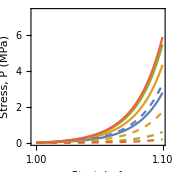

```mathematica
ListLinePlot[Flatten[{Table[biaxPts11[#,λ],{λ,1,1.1,0.001}]&/@{0,1,3,8},Table[biaxPts22[#,λ],{λ,1,1.1,0.001}]&/@{0,1,3,8}},1],PlotRange->{All,{0,7.301383232853702}},
AspectRatio->1,
PlotStyle->{Directive[RGBColor[0.368417, 0.506779, 0.709798]],Directive[RGBColor[0.880722, 0.611041, 0.142051]],Directive[RGBColor[0.560181, 0.691569, 0.194885]],Directive[RGBColor[0.922526, 0.385626, 0.209179]],Directive[RGBColor[0.368417, 0.506779, 0.709798],Dashed],Directive[RGBColor[0.880722, 0.611041, 0.142051],Dashed],Directive[RGBColor[0.560181, 0.691569, 0.194885],Dashed],Directive[RGBColor[0.922526, 0.385626, 0.209179],Dashed]},
Frame->True,
FrameTicks->{{Range[0,7], None},{{{1,"1.00"},1.05,{1.1,"1.10"}},None}},
FrameLabel-> {"Stretch, λ","Stress, P (MPa)"},

BaseStyle->Directive[FontFamily->fonts,FontSize->sizeTicks],
LabelStyle->Directive[FontFamily->fonts,FontSize->sizeLabels,Black],
FrameStyle->Directive[FontFamily->fonts,FontSize->sizeLabels],FrameTicksStyle->Directive[FontFamily->fonts,FontSize->sizeTicks],
ImagePadding->{{sizeLabels+2sizeTicks,1sizeTicks+1},{2sizeLabels+sizeTicks,0.5sizeTicks}},

PlotLegends->Placed[LineLegend[{Directive[RGBColor[0.368417, 0.506779, 0.709798]],Directive[RGBColor[0.880722, 0.611041, 0.142051]],Directive[RGBColor[0.560181, 0.691569, 0.194885]],Directive[RGBColor[0.922526, 0.385626, 0.209179]],Directive[RGBColor[0.368417, 0.506779, 0.709798],Dashing[{0.01,0.01}]],Directive[RGBColor[0.880722, 0.611041, 0.142051],Dashing[{0.01,0.01}]],Directive[RGBColor[0.560181, 0.691569, 0.194885],Dashing[{0.01,0.01}]],Directive[RGBColor[0.922526, 0.385626, 0.209179],Dashing[{0.01,0.01}]]},Range[1,8],LegendLayout->tableL,LegendMarkerSize->sizeLegends],{Left,Top}]
,ImageSize->Floor[(imgWidthTotal-1.5sizeLabels)/3]]
```

#### Figure 4c

```mathematica
k0=0.02;α=4.;κ=0.001;mg=0.005;(*k3=0.05;*)k3=0.;
k1=0.028 3096;k2=5.431*^-4;
Do[
Table[biaxPts11[vonMisesκ,λbi]={0,0},{λbi,1,2.3,0.01}];
Table[biaxPts22[vonMisesκ,λbi]={0,0},{λbi,1,2.3,0.01}];
nfiber =200;
Do[
a0List = {Cos[#/2],Sin[#/2],0.}&/@RandomVariate[VonMisesDistribution[0.,vonMisesκ],nfiber];
Do[biaxPts11[vonMisesκ,λbi]+={λbi,PPelasbi[0.01377909885269147,0.028 3096.391865746513,0.0005430957860466969,λbi,a0List[[ia0]]][[1,1]]}/nfiber;
biaxPts22[vonMisesκ,λbi]+={λbi,PPelasbi[0.01377909885269147,0.028 3096.391865746513,0.0005430957860466969,λbi,a0List[[ia0]]][[2,2]]}/nfiber
,{λbi,1,2.3,0.01}];
,{ia0,1,nfiber}];
,{vonMisesκ,{0,1,3,8}}];
```

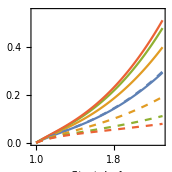

```mathematica
ListLinePlot[Flatten[{Table[biaxPts11[#,λ],{λ,1,2.3,0.011}]&/@{0,1,3,8},Table[biaxPts22[#,λ],{λ,1,2.3,0.01}]&/@{0,1,3,8}},1],PlotRange->{All,{0,0.55}},
AspectRatio->1,
PlotStyle->{Directive[RGBColor[0.368417, 0.506779, 0.709798]],Directive[RGBColor[0.880722, 0.611041, 0.142051]],Directive[RGBColor[0.560181, 0.691569, 0.194885]],Directive[RGBColor[0.922526, 0.385626, 0.209179]],Directive[RGBColor[0.368417, 0.506779, 0.709798],Dashed],Directive[RGBColor[0.880722, 0.611041, 0.142051],Dashed],Directive[RGBColor[0.560181, 0.691569, 0.194885],Dashed],Directive[RGBColor[0.922526, 0.385626, 0.209179],Dashed]},
Frame->True,
FrameTicks->{{{{0,"0.0"},0.1,0.2,0.3,0.4,0.5},None},{{{1,"1.0"},1.4,1.8,2.2},None}},
FrameLabel-> {"Stretch, λ","Stress, P (MPa)"},

BaseStyle->Directive[FontFamily->fonts,FontSize->sizeTicks],
LabelStyle->Directive[FontFamily->fonts,FontSize->sizeLabels,Black],
FrameStyle->Directive[FontFamily->fonts,FontSize->sizeLabels],FrameTicksStyle->Directive[FontFamily->fonts,FontSize->sizeTicks],
ImagePadding->{{sizeLabels+3sizeTicks,1},{2sizeLabels+sizeTicks,0.5sizeTicks}},

PlotLegends->Placed[LineLegend[{Directive[RGBColor[0.368417, 0.506779, 0.709798]],Directive[RGBColor[0.880722, 0.611041, 0.142051]],Directive[RGBColor[0.560181, 0.691569, 0.194885]],Directive[RGBColor[0.922526, 0.385626, 0.209179]],Directive[RGBColor[0.368417, 0.506779, 0.709798],Dashing[{0.01,0.01}]],Directive[RGBColor[0.880722, 0.611041, 0.142051],Dashing[{0.01,0.01}]],Directive[RGBColor[0.560181, 0.691569, 0.194885],Dashing[{0.01,0.01}]],Directive[RGBColor[0.922526, 0.385626, 0.209179],Dashing[{0.01,0.01}]]},Range[1,8],LegendLayout->tableL,LegendMarkerSize->sizeLegends],{Left,Top}]
,ImageSize->Floor[(imgWidthTotal-1.5sizeLabels)/3]]
```

#### Figure 4e

```mathematica
Clear[c,k1,k2,β1,β2,τ1,τ2];
Clear[ε, na0, a0List, CCinv, CCbar, CCbarinv, CCvMinv, I1, I4, I4bar, I4vbar, I4ebar, SSeqIso, SSvisIso, SSeqAni, SSvisAni, SSpres, SSTotal]
(*Parameters*)
c = 0.0012011055940892702(*MPa*);
k1 =0.004 1.3(*MPa*);
k2 = 25;
β1 = 0.;
β2 =10.;
τ1 = 1.;
τ2 = 0.15;
(*Sim paras*)
dε = 0.05;
nt = 100; (*number of time steps*)
dt = dε/nt;
t0 = 0.;
εLoad = 0.1;
nLoad = Ceiling[εLoad/dt];(*iteration steps of loading*)

Do[
nfiber = 200;
na0 = 10.;(* number of fiber's orientations*)
(*von Mises distribution*)a0List = {Cos[#/2],Sin[#/2],0.}&/@RandomVariate[VonMisesDistribution[0.,vonMisesκ],nfiber];
a0Bundle[vonMisesκ]=a0List;
(*a0List = Table[{Cos[(i/(na0+1)-1/2)π],Sin[(i/(na0+1)-1/2)π],0.},{i,na0}];*)
(*Uniaxial Test*)
FF[λ_] := {{λ, 0, 0}, {0, λ, 0}, {0, 0, 1/λ^2}};
CC[λ_] := FF[λ]ᵀ.FF[λ];
(*Initialization*)
CCvMinv[0] = IdentityMatrix[3];
I4vbar[0] = 1.;
I4ebar[0] = 1;
SSTotal[0] = Table[0.,{i,3},{j,3}];
PPTotal[0] = Table[0.,{i,3},{j,3}];
ε[0] = 0.;
For[n = 1, n <= 2nLoad, n++,
 tList[n] = t0 + n*dt;
 If[n <= nLoad,
  ε[n] = ε[n-1] +dt,
  ε[n] = (*ε[10]*)ε[n-1] -dt
  ];
 λ = 1 + ε[n];
 J = 1;
 CCinv[n] = Inverse[CC[λ]];
 CCbar[n] = CC[λ];
 CCbarinv[n] = Inverse[CCbar[n]];
 I1[n] = Tr[CC[λ]];
 (*Incompressible, plane stress*)
 SSeqIso[n] = 2 c(*ψ1bar*) IdentityMatrix[3];solα = NSolve[Det[τ1/(τ1+dt) (CCvMinv[n-1] + α dt CCinv[n])] == 1, α, Reals]; CCvMinv[n] = Evaluate[τ1/(τ1 + dt) (CCvMinv[n-1] + α dt CCinv[n]) /. solα[[1]]];
 CCvM[n] = Inverse[CCvMinv[n]]; SSvisIso[n] = 2 (c β1)(*ψebar*) (CCvMinv[n]); SSeqAni[n] = Table[0.,{i,3},{j,3}]; SSvisAni[n] = Table[0.,{i,3},{j,3}]; For[ia0=1,ia0≤nfiber,ia0++,    a0a0 = Outer[Times,a0List[[ia0]],a0List[[ia0]]];    I4[n] = a0List[[ia0]].CC[λ].a0List[[ia0]];    I4bar[n] = a0List[[ia0]].CCbar[n].a0List[[ia0]];    I4ebar[n-1] = a0List[[ia0]].CCbar[n].a0List[[ia0]]/I4vbar[n-1];    solI4eNew = FindRoot[(I4e - I4ebar[n-1])/dt == (-1/τ2 I4e (E^(k2(I4e-1))-1))/(I4e k2 E^(k2(I4e-1)) + (E^(k2(I4e-1))-1)), {I4e, I4ebar[n-1]}];    I4ebar[n] = Evaluate[I4e /. solI4eNew[[1]]];    I4vbar[n] = I4bar[n]/I4ebar[n];SSeqAni[n] += 2 (k1/2 (E^(k2 (I4[n]-1))-1) )(*ψ4bar*) a0a0;SSvisAni[n] += 2 (β2 k1/2 (E^(k2 (I4ebar[n]-1))-1) )(*ψ4ebar*)I4ebar[n] a0a0/I4bar[n];
 ];
 
 p = -2 c CC[λ][[3,3]] - 2 β1 c CC[λ][[3,3]]/CCvM[n][[3,3]];
 SSpres[n] = p CCinv[n];
 SSTotal[n] = SSeqIso[n] + SSvisIso[n] + (SSeqAni[n] + SSvisAni[n])/nfiber + SSpres[n];
 PPTotal[n]= FF[λ].SSTotal[n];
 σTotal[n] = FF[λ].SSTotal[n].FF[λ]ᵀ;
];
cyclicPts[1,vonMisesκ]=Evaluate[{1+ε[#],PPTotal[#][[1,1]]}&/@Range[0,2nLoad]];
cyclicPts[2,vonMisesκ]=Evaluate[{1+ε[#],PPTotal[#][[2,2]]}&/@Range[0,2nLoad]];
,{vonMisesκ,{0,1,3,8}}];
```

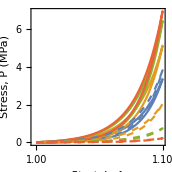

```mathematica
ListLinePlot[Flatten[{Evaluate[cyclicPts[1,#]]&/@{0,1,3,8},Evaluate[cyclicPts[2,#]]&/@{0,1,3,8}},1],PlotRange->All,
AspectRatio->1,
PlotStyle->{Directive[RGBColor[0.368417, 0.506779, 0.709798]],Directive[RGBColor[0.880722, 0.611041, 0.142051]],Directive[RGBColor[0.560181, 0.691569, 0.194885]],Directive[RGBColor[0.922526, 0.385626, 0.209179]],Directive[RGBColor[0.368417, 0.506779, 0.709798],Dashed],Directive[RGBColor[0.880722, 0.611041, 0.142051],Dashed],Directive[RGBColor[0.560181, 0.691569, 0.194885],Dashed],Directive[RGBColor[0.922526, 0.385626, 0.209179],Dashed]},
Frame->True,
FrameTicks->{{Range[0,7], None},{{{1,"1.00"},1.05,{1.1,"1.10"}},None}},
FrameLabel-> {"Stretch, λ","Stress, P (MPa)"},

BaseStyle->Directive[FontFamily->fonts,FontSize->sizeTicks],
LabelStyle->Directive[FontFamily->fonts,FontSize->sizeLabels,Black],
FrameStyle->Directive[FontFamily->fonts,FontSize->sizeLabels],FrameTicksStyle->Directive[FontFamily->fonts,FontSize->sizeTicks],
ImagePadding->{{sizeLabels+2sizeTicks,1sizeTicks+1},{2sizeLabels+sizeTicks,0.5sizeTicks}},

PlotLegends->Placed[LineLegend[{Directive[RGBColor[0.368417, 0.506779, 0.709798]],Directive[RGBColor[0.880722, 0.611041, 0.142051]],Directive[RGBColor[0.560181, 0.691569, 0.194885]],Directive[RGBColor[0.922526, 0.385626, 0.209179]],Directive[RGBColor[0.368417, 0.506779, 0.709798],Dashing[{0.01,0.01}]],Directive[RGBColor[0.880722, 0.611041, 0.142051],Dashing[{0.01,0.01}]],Directive[RGBColor[0.560181, 0.691569, 0.194885],Dashing[{0.01,0.01}]],Directive[RGBColor[0.922526, 0.385626, 0.209179],Dashing[{0.01,0.01}]]},Range[1,8],LegendLayout->tableL,LegendMarkerSize->sizeLegends],{Left,Top}]
,ImageSize->Floor[(imgWidthTotal-1.5sizeLabels)/3]]
```

#### Figure 4f

```mathematica
Clear[c,k1,k2,β1,β2,τ1,τ2];
Clear[ε, na0, a0List, CCinv, CCbar, CCbarinv, CCvMinv, I1, I4, I4bar, I4vbar, I4ebar, SSeqIso, SSvisIso, SSeqAni, SSvisAni, SSpres, SSTotal]
(*Parameters*)
c = 0.01377909885269147;
k1 =0.028 0.31(*MPa*);
k2 = 0.5;
β1 = 0.;
β2 =20.;
τ1 = 1.;
τ2 =0.5;
(*κ = 1*^6(*MPa*);*)
(*Sim paras*)
dε = 0.1;
nt = 10; (*number of time steps*)
dt = dε/nt;
t0 = 0.;
εLoad = 1.3;
nLoad = Ceiling[εLoad/dt];(*iteration steps of loading*)

Do[
nfiber = 200;
na0 = 10.;(* number of fiber's orientations*)
(*von Mises distribution*)a0List = {Cos[#/2],Sin[#/2],0.}&/@RandomVariate[VonMisesDistribution[0.,vonMisesκ],nfiber];
a0Bundle[vonMisesκ]=a0List;
(*a0List = Table[{Cos[(i/(na0+1)-1/2)π],Sin[(i/(na0+1)-1/2)π],0.},{i,na0}];*)
(*Biaxial Test*)
FF[λ_] := {{λ, 0, 0}, {0, λ, 0}, {0, 0, 1/λ^2}};
CC[λ_] := FF[λ]ᵀ.FF[λ];
(*Initialization*)
CCvMinv[0] = IdentityMatrix[3];
I4vbar[0] = 1.;
I4ebar[0] = 1;
SSTotal[0] = Table[0.,{i,3},{j,3}];
PPTotal[0] = Table[0.,{i,3},{j,3}];
ε[0] = 0.;
For[n = 1, n <= 2nLoad, n++,
 tList[n] = t0 + n*dt;
 If[n <= nLoad,
  ε[n] = ε[n-1] +dt,
  ε[n] = (*ε[10]*)ε[n-1] -dt
  ];
 λ = 1 + ε[n];
 J = 1;
 CCinv[n] = Inverse[CC[λ]];
 CCbar[n] = CC[λ];
 CCbarinv[n] = Inverse[CCbar[n]];
 I1[n] = Tr[CC[λ]];
 (*Incompressible, plane stress*)
 SSeqIso[n] = 2 c(*ψ1bar*) IdentityMatrix[3];
solα = NSolve[Det[τ1/(τ1+dt) (CCvMinv[n-1] + α dt CCinv[n])] == 1, α, Reals];
 CCvMinv[n] = Evaluate[τ1/(τ1 + dt) (CCvMinv[n-1] + α dt CCinv[n]) /. solα[[1]]];
 CCvM[n] = Inverse[CCvMinv[n]];
 SSvisIso[n] = 2 (c β1)(*ψebar*) (CCvMinv[n]);
 
 SSeqAni[n] = Table[0.,{i,3},{j,3}];
 SSvisAni[n] = Table[0.,{i,3},{j,3}];
 For[ia0=1,ia0≤nfiber,ia0++,
    a0a0 = Outer[Times,a0List[[ia0]],a0List[[ia0]]];
    I4[n] = a0List[[ia0]].CC[λ].a0List[[ia0]];
    I4bar[n] = a0List[[ia0]].CCbar[n].a0List[[ia0]];
    I4ebar[n-1] = a0List[[ia0]].CCbar[n].a0List[[ia0]]/I4vbar[n-1];
    solI4eNew = FindRoot[(I4e - I4ebar[n-1])/dt == (-1/τ2 I4e (E^(k2(I4e-1))-1))/(I4e k2 E^(k2(I4e-1)) + (E^(k2(I4e-1))-1)), {I4e, I4ebar[n-1]}];
    I4ebar[n] = Evaluate[I4e /. solI4eNew[[1]]];
    I4vbar[n] = I4bar[n]/I4ebar[n];
    
    SSeqAni[n] += 2 (k1/2 (E^(k2 (I4[n]-1))-1) )(*ψ4bar*) a0a0;
    
    SSvisAni[n] += 2 (β2 k1/2 (E^(k2 (I4ebar[n]-1))-1) )(*ψ4ebar*)I4ebar[n] a0a0/I4bar[n];
 ];
 
 p = -2 c CC[λ][[3,3]] - 2 β1 c CC[λ][[3,3]]/CCvM[n][[3,3]];
 SSpres[n] = p CCinv[n];
 SSTotal[n] = SSeqIso[n] + SSvisIso[n] + (SSeqAni[n] + SSvisAni[n])/nfiber + SSpres[n];
 PPTotal[n]= FF[λ].SSTotal[n];
 σTotal[n] = FF[λ].SSTotal[n].FF[λ]ᵀ;
];
cyclicPts[1,vonMisesκ]=Evaluate[{1+ε[#],PPTotal[#][[1,1]]}&/@Range[0,2nLoad]];
cyclicPts[2,vonMisesκ]=Evaluate[{1+ε[#],PPTotal[#][[2,2]]}&/@Range[0,2nLoad]]
,{vonMisesκ,{0,1,3,8}}];
```

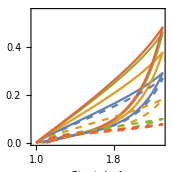

```mathematica
ListLinePlot[Flatten[{Evaluate[cyclicPts[1,#]]&/@{0,1,3,8},Evaluate[cyclicPts[2,#]]&/@{0,1,3,8}},1],PlotRange->{All,{0,0.55}},
AspectRatio->1,
PlotStyle->{Directive[RGBColor[0.368417, 0.506779, 0.709798]],Directive[RGBColor[0.880722, 0.611041, 0.142051]],Directive[RGBColor[0.560181, 0.691569, 0.194885]],Directive[RGBColor[0.922526, 0.385626, 0.209179]],Directive[RGBColor[0.368417, 0.506779, 0.709798],Dashed],Directive[RGBColor[0.880722, 0.611041, 0.142051],Dashed],Directive[RGBColor[0.560181, 0.691569, 0.194885],Dashed],Directive[RGBColor[0.922526, 0.385626, 0.209179],Dashed]},
Frame->True,
FrameTicks->{{{{0,"0.0"},0.1,0.2,0.3,0.4,0.5},None},{{{1,"1.0"},1.4,1.8,2.2},None}},
FrameLabel-> {"Stretch, λ","Stress, P (MPa)"},

BaseStyle->Directive[FontFamily->fonts,FontSize->sizeTicks],
LabelStyle->Directive[FontFamily->fonts,FontSize->sizeLabels,Black],
FrameStyle->Directive[FontFamily->fonts,FontSize->sizeLabels],FrameTicksStyle->Directive[FontFamily->fonts,FontSize->sizeTicks],
ImagePadding->{{sizeLabels+3sizeTicks,1},{2sizeLabels+sizeTicks,0.5sizeTicks}},

PlotLegends->Placed[LineLegend[{Directive[RGBColor[0.368417, 0.506779, 0.709798]],Directive[RGBColor[0.880722, 0.611041, 0.142051]],Directive[RGBColor[0.560181, 0.691569, 0.194885]],Directive[RGBColor[0.922526, 0.385626, 0.209179]],Directive[RGBColor[0.368417, 0.506779, 0.709798],Dashing[{0.01,0.01}]],Directive[RGBColor[0.880722, 0.611041, 0.142051],Dashing[{0.01,0.01}]],Directive[RGBColor[0.560181, 0.691569, 0.194885],Dashing[{0.01,0.01}]],Directive[RGBColor[0.922526, 0.385626, 0.209179],Dashing[{0.01,0.01}]]},Range[1,8],LegendLayout->tableL,LegendMarkerSize->sizeLegends],{Left,Top}]
,ImageSize->Floor[(imgWidthTotal-1.5sizeLabels)/3]]
```

### Figure 5

```mathematica
(*Solvers definiation*)
bisectionSolver[a0_,b0_,func_,tol_,varSol_]:=Module[{a1=a0,b1=b0,aint,fa,fb,fint,iter},
iter=0;
fa=func[a1];
fb=func[b1];
If[fa fb>= 0,Print["Invalid a0, b0!"];Abort[]];
aint=(a1+b1)/2.;
fint=func[aint];
While[Abs[fint]>tol&&iter<100,
If[fa fint>0,a1=aint;fa=fint,b1=aint;fb=fint];
aint=(a1+b1)/2.;
fint=func[aint];
iter++;
];
If[iter==200,Print["Bisection Solver Reach max iteration number"]];
varSol=aint;
];
ϕbGenerator[k1_(*MPa*),k2_,CSArea_(*nm^2*),l0_(*μm*),fTypical_(*pN*)]:=Module[{λList,λi,initEnergy,infiEnergy,dataLine},
(*Parameters*)
rIntegrinsLigand=1.;
kBT=4.28317 10^-3(*pN·μm*);
Kon=0.01;(*1/s*)
hatKoff=0.012;(*1/s*)

(*Generate discrete ΔE(λ)*)
λList=Range[1,2.,0.01];

(*Reset data collection variable*)
phaseData={};

Do[
λi=λList[[i]];
ψf[I1_,I4_]:=k1/(2 k2) (E^(k2 (I4-1))-k2(I4-1)-1);
P11elas[λ_]:=λ k1(E^(k2 (λ^2 -1))-1);
solλelas=FindRoot[(P11elas[λt] -P11elas[λi])CSArea==fTypical,{λt,λi}];
λdeformed[λi]=Evaluate[λt/.solλelas[[1]]];
EmHGOels[λ_]:=ψf[λ^2+2/λ,λ^2](*MPa*)CSArea(*nm^2*) l0(*μm*);
initEnergy=EmHGOels[λi];
infiEnergy=EmHGOels[λdeformed[λi]];
(*Solve ODE*)
(*Subscript[n, Integrin]=Subscript[n, ligand];Overscript[Subscript[ϕ, b], .]=Subscript[K, on](1-Subscript[ϕ, b])-Subscript[K, off]Subscript[ϕ, b];*)

(*Purely Elastic Part*)
(*ΔEelas[λi]=infiEnergy-initEnergy;*)
ΔEelas[λi]=fTypical l0(λdeformed[λi]-λi);
KoffElas=hatKoff E^(ΔEelas[λi]/kBT);
ϕbElasODE=NDSolve[{ϕbODE'[t]==rIntegrinsLigand Kon(1-ϕbODE[t])-KoffElas ϕbODE[t],ϕbODE[0]==0},ϕbODE[t],{t,0,3600}];
ρbElas=ϕbODE[t]/.ϕbElasODE[[1]]/.t->3600;

(*Collect results*)
dataLine={(*η,*)λi,ρbElas,(*ρbVisc,*)(*τoff,*)1/hatKoff};
AppendTo[phaseData,dataLine];
(*Print[dataLine];*)

,{i,1,Length[λList]}]
];

(*Start solving*)
nθ = 20;
ρiList=Range[500,5000,500];
κList={0,1,2};
fmList={5,6,7,8,9,10,11,12};
l0List=Range[0.05,1,0.05];

SetSharedVariable[solλxy];
solλxy={};
ParallelDo[
(*von Mises distribution*)
Pθ=Table[2PDF[VonMisesDistribution[0,vonMisesκ]][2θ]π/nθ,{θ,-π/2+π/nθ/2,π/2-π/nθ/2,π/nθ}];
(*Collagen*)
(*ϕbGenerator[0.004 17.599164683153674(*MPa*),20.81811370546901,17000.(*nm^2*),l0(*μm*),fm(*pN*)];*)
(*Fibrin*)
ϕbGenerator[0.028 3096.391865746513,0.0005430957860466969,π (390/2)^2(*nm^2*),l0(*μm*),fm(*pN*)];

ϕbVSλ[fm]=phaseData[[All,1;;2]];
ϕbFunction[fm]=Interpolation[ϕbVSλ[fm],InterpolationOrder->2];
FF[λx_,λy_]:={{λx,0,0},{0,λy,0},{0,0,1/(λx λy)}};
CC[λx_,λy_]:=FF[λx,λy]ᵀ . FF[λx,λy];
I4[λx_,λy_,a0_]:=a0 . CC[λx,λy] . a0;
SSact[ζ_,fm_,ρi_,λx_,λy_,a0_]:=10^(-6)ζ fm ρi ϕbFunction[fm][Sqrt[I4[λx,λy,a0]]]Outer[Times,a0,a0]/Tr[Outer[Times,FF[λx,λy] . a0,FF[λx,λy] . a0]];
SSactc[ζ_,fm_,ρi_,λx_,λy_,a0_]:=10^(-6) ζ fm ρi ϕbFunction[fm][1]Outer[Times,a0,a0]/Tr[Outer[Times,FF[λx,λy] . a0,FF[λx,λy] . a0]];
SSpas[k0e_,k1e_,k2e_,λx_,λy_,a0_]:=2 k0e IdentityMatrix[3]+ 2 (k1e/2 (E^(k2e (a0 . CC[λx,λy] . a0-1))-1) ) Outer[Times,a0,a0] -2k0e CC[λx,λy][[3,3]]Inverse[CC[λx,λy]];
SSpasc[k0e_,k1e_,k2e_,λx_,λy_,a0_]:=2 k0e IdentityMatrix[3] -2k0e CC[λx,λy][[3,3]]Inverse[CC[λx,λy]];

stressRes[k0e_,k1e_,k2e_,ζ_,fm_,ρi_,λx_,λy_,a0_]:=Piecewise[{{SSact[ζ,fm,ρi,λx,λy,a0]+SSpas[k0e,k1e,k2e,λx,λy,a0],I4[λx,λy,a0]>1},{SSactc[ζ,fm,ρi,λx,λy,a0]+SSpasc[k0e,k1e,k2e,λx,λy,a0],I4[λx,λy,a0]<= 1}}];
statStrsRes1[k0e_,k1e_,k2e_,ζ_,fm_,ρi_,λx_,λy_,a0List_]:=Total[Pθ[[#]]stressRes[k0e,k1e,k2e,ζ,fm,ρi,λx,λy,a0List[[#]]][[1,1]]&/@Range[1,nθ]];
statStrsRes2[k0e_,k1e_,k2e_,ζ_,fm_,ρi_,λx_,λy_,a0List_]:=Total[Pθ[[#]]stressRes[k0e,k1e,k2e,ζ,fm,ρi,λx,λy,a0List[[#]]][[2,2]]&/@Range[1,nθ]];

Module[{k0e,k1e,k2e,ζ,xa,xb,xint,ya,yb,tol,iter,fa1,fa2,fb1,fb2,fint1,fint2},
k0e=0.01377909885269147;
k1e=0.028 3096.391865746513;
k2e=0.0005430957860466969;
ζ=0.29;

xa=0.5;
xb=1.;
ya=0.3;
yb=1.5;
iter=0;
tol=1*^-6;
Clear[fa1,fa2,fb1,fb2];bisectionSolver[ya,yb,statStrsRes1[k0e,k1e,k2e,ζ,fm,ρi,xa,#,a0List]&,tol,fa1];
bisectionSolver[ya,yb,statStrsRes2[k0e,k1e,k2e,ζ,fm,ρi,xa,#,a0List]&,tol,fa2];
bisectionSolver[ya,yb,statStrsRes1[k0e,k1e,k2e,ζ,fm,ρi,xb,#,a0List]&,tol,fb1];
bisectionSolver[ya,yb,statStrsRes2[k0e,k1e,k2e,ζ,fm,ρi,xb,#,a0List]&,tol,fb2];
If[(fa1-fa2)(fb1-fb2)>= 0,Print["Invalid xa, xb!"];Print[TableForm[{fa1,fa2,fb1,fb2}]];Abort[]];
xint=(xa+xb)/2.;
Clear[fint1,fint2];
bisectionSolver[ya,yb,statStrsRes1[k0e,k1e,k2e,ζ,fm,ρi,xint,#,a0List]&,tol,fint1];
bisectionSolver[ya,yb,statStrsRes2[k0e,k1e,k2e,ζ,fm,ρi,xint,#,a0List]&,tol,fint2];
While[Abs[fint1-fint2]>tol&&iter<200,
If[(fa1-fa2)(fint1-fint2)>0,
xa=xint;
Clear[fa1,fa2];
bisectionSolver[ya,yb,statStrsRes1[k0e,k1e,k2e,ζ,fm,ρi,xa,#,a0List]&,tol,fa1];
bisectionSolver[ya,yb,statStrsRes2[k0e,k1e,k2e,ζ,fm,ρi,xa,#,a0List]&,tol,fa2];,
xb=xint;Clear[fb1,fb2];
bisectionSolver[ya,yb,statStrsRes1[k0e,k1e,k2e,ζ,fm,ρi,xb,#,a0List]&,tol,fb1];
bisectionSolver[ya,yb,statStrsRes2[k0e,k1e,k2e,ζ,fm,ρi,xb,#,a0List]&,tol,fb2];
];
xint=(xa+xb)/2.;
Clear[fint1,fint2];
bisectionSolver[ya,yb,statStrsRes1[k0e,k1e,k2e,ζ,fm,ρi,xint,#,a0List]&,tol,fint1];
bisectionSolver[ya,yb,statStrsRes2[k0e,k1e,k2e,ζ,fm,ρi,xint,#,a0List]&,tol,fint2];
iter++;
];
If[iter==200,Print["Reach max iteration number"]];
AppendTo[solλxy,{vonMisesκ,fm,ρi,l0,xint,(fint1+fint2)/2.}]
]
,{vonMisesκ,κList},{ρi,{500}},{fm,{7}},{l0,l0List}];
Export["HomoSolData.dat",solλxy];
```

### Figure S1 (Toggle comment under “Collagen” and “Fibrin” to run difference cases)

#### Hyperelastic model

```mathematica
Module[{λList,λi,initEnergy,infiEnergy,dataLine},
(*Parameters*)
rIntegrinsLigand=1.;
kBT=4.28317 10^-3(*pN·μm*);
Kon=0.002;(*1/s*)
hatKoff=0.012;(*1/s*)

l0=0.1(*μm*);

(*Collagen*)
k1=0.004 17.599164683153674*^6(*Pa*);
k2=20.81811370546901;
CSArea=17000*^-6(*μm^2*);
(*(*Fibrin*)
k1=0.028 3096.391865746513*^6(*Pa*);
k2=0.0005430957860466969;
CSArea=π (390/2)^2*10^-6(*μm^2*);
*)
(*Generate discrete ΔE(λ)*)
λList=Range[1,1.1,0.001];
phaseData={};

Do[
λi=λList[[i]];
ψf[I4_]:=k1/(2 k2) (E^(k2 (I4-1))-k2(I4-1)-1);
P11elas[λ_]:=λ k1(E^(k2 (λ^2 -1))-1);
solλelas=FindRoot[{(P11elas[λt] -P11elas[λi])CSArea==f0/(1-β+(ka/(2(ψf[λt^2]-ψf[λi^2])CSArea/((λt-λi)^2 l0))+ka/kN))},{λt,λi+0.001}];

fa[λi]=f0/(1-β+(ka/(2(ψf[λt^2]-ψf[λi^2])CSArea/((λt-λi)^2 l0))+ka/kN))/.solλelas;

(*Collect results*)
dataLine={λi,fa[λi],ka,kN,β,f0};
AppendTo[phaseData,dataLine];
(*Print[dataLine];*)

,{i,1,Length[λList]},{ka,{20*^3,50*^3}},{kN,{1*^3,4*^3,10*^3}},{β,{0,0.5,0.8,1}},{f0,{100,200}}]
]
```

#### Hyper-viscoelastic model

```mathematica
Clear[c,k1,k2,β1,β2,τ1,τ2];
Clear[ε, na0, a0List, CCinv, CCbar, CCbarinv, CCvMinv, I1, I4, I4bar, I4vbar, I4ebar, SSeqIso, SSvisIso, SSeqAni, SSvisAni, SSpres, SSTotal];

(*Parameters*)
rIntegrinsLigand=1.;
kBT=4.28317 10^-3(*pN·μm*);
Kon=0.01;(*1/s*)
hatKoff=0.012;(*1/s*)

c = 0.00(*MPa*);
(*Collagen*)
k1 = 0.004 1.3(*MPa*);
k2 = 25;
β1 = 0.;
β2 = 10.;
τ1 = 1.;
τ2 = 0.15;
CSArea=17000(*nm^2*);
(*(*Fibrin*)
k1 =0.028 0.31(*MPa*);
k2 = 0.5;
β1 = 0.;
β2 =20.;
τ1 = 1.;
τ2 =0.5(*s*);
CSArea=π (390/2)^2(*nm^2*);*)

a0= {1,0,0};

(*Define functions*)
ψf[I1_,Ie_,I4_,I4e_]:=c(I1-3)+β1 c(Ie-3)+k1/(2 k2) (E^(k2 (I4-1))-k2(I4-1)-1)+β2 k1/(2 k2) (E^(k2 (I4e-1))-k2(I4e-1)-1) ;
S11[λt_,λv_]:=(2c IdentityMatrix[3]-2c (1/λt)Inverse[CC[λt]]+k1(E^(k2 (λt^2 a0[[1]]^2-1))-1)Outer[Times,a0,a0]+β2 k1 (E^(k2 (λt^2/λv^2-1))-1) Outer[Times,a0,a0]/(λv^2 a0[[1]]^2))[[1,1]];
P11[λt_,λv_]:=λt S11[λt,λv];

(*Sim paras*)
(*df =0.1; (*Force loading rate, [pN/s]*)*)
Δt = 0.01;(*time interval, [s]*)
(*f0 = 0.;(*Initial force, [pN]*)
fMax =7;(*Max loading force, [pN]*)
nLoad = Ceiling[(fMax-f0)/((*df*) Δt)]*);(*iteration steps of loading*)
tTotal=30;
nTime=Ceiling[tTotal/Δt];
tolE=10*^-7;

(*Reset data collection variable*)
SetSharedVariable[phaseData,dataLine];
phaseData={};
ParallelDo[
(*Uniaxial Test*)
FF[λ_] := {{λ, 0, 0}, {0, 1/Sqrt[λ](*λ*), 0}, {0, 0, 1/Sqrt[λ](*1/λ^2*)}};
CC[λ_] := FF[λ]ᵀ . FF[λ];
(*Initialization*)
CCvMinv[0] = IdentityMatrix[3];
λtot[0] = λi;(*initial total stretch*)
λv[0] = λi;
λe[0] = λtot[0]/λv[0];
(*ft[0] = f0;*)
tList[0] = 0;
SSTotal[0] = Table[0.,{i,3},{j,3}];
PPTotal[0] = Table[0.,{i,3},{j,3}];
EmHGOvis[0]=ψf[λtot[0]^2+2/λtot[0],λe[0]^2+2/λe[0],λtot[0]^2,λe[0]^2] CSArea l0;

For[n=1, n<=nTime, n++,
tList[n] = n*Δt;
J = 1;

a0a0 = Outer[Times,a0,a0];
I4bar0 = a0 . CC[λtot[n-1]] . a0;
I4vbar0=a0 . CC[λv[n-1]] . a0;

(*Piecewise loading function*)
(*If[n≤ nLoad,ft[n]=f0+n df Δt,ft[n]=fMax];*)

(*Force balance equation*)
solI4eTest=FindRoot[(P11[λtot1,λv[n-1]]-P11[λtot[0],λtot[0]])CSArea==f0/(1-β+(ka/(2(ψf[λtot1^2+2/λtot1,λtot[0]^2+2/λtot[0],λtot1^2,λtot[0]^2]-ψf[λtot[0]+2/Sqrt[λtot[0]],λtot[0]+2/Sqrt[λtot[0]],λtot[0]^2,λtot[0]^2])CSArea/((λtot1-λtot[0])^2 l0))+ka/kN)),{λtot1,λtot[n-1]+0.001}];
λtot[n]=Evaluate[λtot1/.solI4eTest];
λe[n-1]=λtot[n]/λv[n-1];
I4ebar0 = a0 . CC[λe[n-1]] . a0;

(*Viscous equation*)
solI4eNew = FindRoot[
(λe1^2 - I4ebar0)/Δt == (-1/τ2 λe1^2 (E^(k2(λe1^2-1))-1))/(λe1^2 k2 E^(k2(λe1^2-1)) + (E^(k2(λe1^2-1))-1))
,{λe1,λe[n-1]}];
λe[n]=Evaluate[λe1/.solI4eNew];(*Update Subscript[λ, e]*)
λv[n] = λtot[n]/λe[n];
EmHGOvis[n]=ψf[λtot[n]^2+2/λtot[n],λe[n]^2+2/λe[n],λtot[n]^2,λe[n]^2] CSArea l0;
If[Abs[EmHGOvis[n]-EmHGOvis[n-1]]<tolE,nEq=n;tolE=-10];
];
initEnergy=EmHGOvis[0];
infiEnergy=EmHGOvis[nTime];
intmEnergy[CI_]:=(1-CI) initEnergy+CI infiEnergy;
EmIntp=Interpolation[{tList[#],EmHGOvis[#]}&/@Range[0,nTime]];
τoff=tList[nEq];
Koffvisc[tvisc_]:=hatKoff E^((EmIntp[tvisc]-initEnergy)/kBT);
Poffvisc[tvisc_]:=E^(-NIntegrate[Koffvisc[y],{y,0,tvisc}]);
Poffintp=Interpolation[Table[{dt,Poffvisc[dt]},{dt,0,τoff,τoff/100}]];
τoffAvg=NIntegrate[ tv Poffintp[tv],{tv,0,τoff}]/NIntegrate[ Poffintp[tv],{tv,0,τoff}];
ϕbViscODE=NDSolve[{ϕbODE'[t]==rIntegrinsLigand Kon(1-ϕbODE[t])-Koffvisc[τoffAvg] ϕbODE[t],ϕbODE[0]==0},ϕbODE[t],{t,0,tList[nTime]}];
ρbVisc=ϕbODE[t]/.ϕbViscODE[[1]]/.t->tList[nTime];
{λAvg,λvAvg}={Interpolation[{tList[#],λtot[#]}&/@Range[0,nTime]][τoffAvg],Interpolation[{tList[#],λtot[#]}&/@Range[0,nTime]][τoffAvg]};
fa[λi]=f0/(1-β+(ka/(2(ψf[λAvg^2+2/λAvg,λAvg^2/λvAvg^2+2/(λAvg/λvAvg),λAvg^2,λAvg^2/λvAvg^2]-ψf[λtot[0]^2+2/λtot[0],λtot[0]^2+2/λtot[0],λtot[0]^2,λtot[0]^2])CSArea/((λAvg-λtot[0])^2 l0))+ka/kN));
(*Collect results*)
dataLine={λi,fa[λi],ka,kN,β,f0};
AppendTo[phaseData,dataLine];
,{λi,1,1.1,0.001},{ka,{20*^3,50*^3}},{kN,{1*^3,4*^3,10*^3}},{β,{0,0.5,0.8,1}},{f0,{100,200}}]
Export[FileNameJoin[Directory[]<>"/faVsLambda_visc_Collagen.txt"],phaseData,"Table"]
```

```mathematica
phaseData=Import[FileNameJoin[Directory[]<>"/faVsLambda_visc_Collagen.txt"],"Table"];
phaseData=Sort[Sort[Sort[Sort[Sort[phaseData,#1[[1]]<#2[[1]]&],#1[[3]]<#2[[3]]&],#1[[4]]<#2[[4]]&],#1[[5]]<#2[[5]]&],#1[[6]]<#2[[6]]&];
```

### Figure S2

#### Collagen

```mathematica
(*Seliktar, DOI:10.1115/1.1449904*)
dataεCol={0.019747769977507046,0.032423270469944754,0.04496884611095231,0.05736615822682967,0.06962675655409423,0.0817396126095562,0.09377593511348326,0.10566910587091027,0.11479840353380344,0.12077813566969398,0.12577208608347878,0.1295176122782722,0.13535362742904944,0.13862477566128528,0.14084871569078916,0.14307559480246557,0.14734009557048466,0.15648134928914637,0.152158205694362,0.16309041800432356,0.16978451510334813,0.17543277382510403,0.18227126824852924,0.18991957026801987};
dataPCol={0.00012374538532533563,0.00022508219889247628,0.0004721891125141582,0.0007561740938456971,0.0011186712096740337,0.0014851740466501654,0.0022161975080756805,0.0029472209695011954,0.0037026779533917884,0.004829810798338712,0.0058826877595754504,0.00704903812874942,0.007861855387632673,0.008874356469197046,0.009823526548800185,0.010816759561029073,0.011822825334563913,0.0144088078997462,0.013192864559298571,0.015130157259460085,0.016248651649746194,0.017303815038071067,0.018284263303897305,0.01860215736040609};
```

```mathematica
ptlist={};
λ0guess=1.;
Do[
Module[{k0=0.001,α=2.2,κ=0.0001,mg=2,k3=0.1,k1=0.00008153605475617464,k2=16.240490104015972,pts,λ1,λ2,λ3,J,ζij},
J[λa_,λs_,λn_]:=λa λs λn;
ζij[λ1_,λ2_,λ3_]:=λ1^2 λ2^(2+α)+λ1^2 λ3^(2+α)+λ2^2 λ3^(2+α)+λ2^2 λ1^(2+α)+λ3^2 λ1^(2+α)+λ3^2 λ2^(2+α);
S11[λ1_,λ2_,λ3_]:=k0 -(k0+2κ J[λ1,λ2,λ3](J[λ1,λ2,λ3]-1))/λ1^2+k1( ⅇ^(k2(λ1^2-1))-1)+2k3 If[ζij[λ1,λ2,λ3]>6, ⅇ^(mg(ζij[λ1,λ2,λ3]-6))-1,0](λ2^(2+α)+λ3^(2+α)+(2+α)/2 λ1^α(λ2^2+λ3^2));
S33[λ1_,λ2_,λ3_]:=k0 -(k0+2κ J[λ1,λ2,λ3](J[λ1,λ2,λ3]-1))/λ3^2+2k3 If[ζij[λ1,λ2,λ3]>6, ⅇ^(mg(ζij[λ1,λ2,λ3]-6))-1,0](λ1^(2+α)+λ2^(2+α)+(2+α)/2 λ3^α(λ1^2+λ2^2));
pts={λ,Abs@λT}/.FindRoot[Evaluate[S33[λ,λT,λT]],{λT,λ0guess},MaxIterations->1000];
λ0guess=pts[[2]];
AppendTo[ptlist,pts];
]
,{λ,1,1.5,0.02}];
intpFunc=Interpolation[ptlist,InterpolationOrder->1];
```

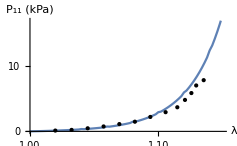
{-Graphics-,-Graphics-}

```mathematica
{ListPlot[{Table[{λ,1000λ S11[λ,intpFunc[λ],intpFunc[λ]]},{λ,1,1.15,0.002}],{dataεCol+1,1000dataPCol(*kPa*)}ᵀ[[1;;13]]},PlotRange->{{1,1.15},{0,17}},Joined->{True,False},PlotStyle->{Automatic,Directive[Black,PointSize[Medium]]},

AxesLabel->{"λ","P_11 (kPa)"},Ticks->{{{1,"1.00"},1.05,{1.1,"1.10"},1.15},{0,5,10,15}},
AxesStyle->Directive[Black,Thickness[Medium]],

BaseStyle->Directive[FontFamily->fonts,FontSize->sizeTicks],
LabelStyle->Directive[FontFamily->fonts,FontSize->sizeLabels,Black],
FrameStyle->Directive[FontFamily->fonts,FontSize->sizeLabels],FrameTicksStyle->Directive[FontFamily->fonts,FontSize->sizeTicks],

PlotLegends->Placed[{"Model","Exp. data"},{Left,Top}],

ImagePadding->{{2.5sizeLabels,1.5sizeLabels},{1.5sizeLabels,2sizeLabels}},
ImageSize->Floor[(imgWidthTotal-1.5sizeLabels)/2]],
Show[ListLinePlot[ptlist,
PlotRange->{{1,1.15},{0.9,1}},
Ticks->{{{1,"1.00"},1.05,{1.1,"1.10"},1.15},{{0.9,"0.90"},0.92,0.94,0.96,0.98,{1,"1.00"}}},
AxesLabel->{"λ","λ^*"},
AxesStyle->Directive[Black,Thickness[Medium]],

BaseStyle->Directive[FontFamily->fonts,FontSize->sizeTicks],
LabelStyle->Directive[FontFamily->fonts,FontSize->sizeLabels,Black],
FrameStyle->Directive[FontFamily->fonts,FontSize->sizeLabels],FrameTicksStyle->Directive[FontFamily->fonts,FontSize->sizeTicks],
ImagePadding->{{2.5sizeLabels,1.5sizeLabels},{1.5sizeLabels,2sizeLabels}}],Plot[{(*intpFunc[λ],*)Callout[1/(√λ),"Incompressible",{1.07,0.97}]},{λ,1,1.15},PlotStyle->Dashed],ImageSize->Floor[(imgWidthTotal-1.5sizeLabels)/2]]
}
```

#### Fibrin

```mathematica
dataPFb={0,0.011264365,0.029217259,0.050167308,0.068203642,0.084714697,0.039810768,0.021664294,0.009088256,0.001388437,-0.005670565};
dataεFb={0,0.065003495,0.147508404,0.230145631,0.308109297,0.376017716,0.321212846,0.241817423,0.158838909,0.085545762,0.009801349};
```

```mathematica
ptlist={};
λ0guess=1.;
Do[
Module[{k0=0.02,α=2.2,κ=0.001,mg=2,k3=0.1,k1=0.028 3096,k2=5.431*^-4,pts,λ1,λ2,λ3,J,ζij},
J[λa_,λs_,λn_]:=λa λs λn;
ζij[λ1_,λ2_,λ3_]:=λ1^2 λ2^(2+α)+λ1^2 λ3^(2+α)+λ2^2 λ3^(2+α)+λ2^2 λ1^(2+α)+λ3^2 λ1^(2+α)+λ3^2 λ2^(2+α);
S11[λ1_,λ2_,λ3_]:=k0 -(k0+2κ J[λ1,λ2,λ3](J[λ1,λ2,λ3]-1))/λ1^2+k1( ⅇ^(k2(λ1^2-1))-1)+2k3 If[ζij[λ1,λ2,λ3]>6, ⅇ^(mg(ζij[λ1,λ2,λ3]-6))-1,0](λ2^(2+α)+λ3^(2+α)+(2+α)/2 λ1^α(λ2^2+λ3^2));
S33[λ1_,λ2_,λ3_]:=k0 -(k0+2κ J[λ1,λ2,λ3](J[λ1,λ2,λ3]-1))/λ3^2+2k3 If[ζij[λ1,λ2,λ3]>6, ⅇ^(mg(ζij[λ1,λ2,λ3]-6))-1,0](λ1^(2+α)+λ2^(2+α)+(2+α)/2 λ3^α(λ1^2+λ2^2));
pts={λ,Abs@λT}/.FindRoot[Evaluate[S33[λ,λT,λT]],{λT,λ0guess},MaxIterations->1000];
λ0guess=pts[[2]];
AppendTo[ptlist,pts];
]
,{λ,1,2.2,0.02}];
intpFunc=Interpolation[ptlist,InterpolationOrder->1];
```

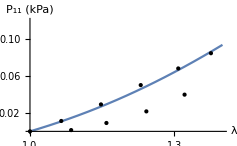
{-Graphics-,-Graphics-}

```mathematica
{ListPlot[{Table[{λ,λ S11[λ,intpFunc[λ],intpFunc[λ]]},{λ,1,1.4,0.02}],{dataεFb+1,dataPFb(*MPa*)}ᵀ(*[[1;;13]]*)},PlotRange->{{1,1.4},{0,0.12}},Joined->{True,False},PlotStyle->{Automatic,Directive[Black,PointSize[Medium]]},

AxesLabel->{"λ","P_11 (kPa)"},Ticks->{{{1,"1.0"},1.1,1.2,1.3,1.4,1.6,1.8,{2,"2.0"},2.2},{0.02,0.04,0.06,0.08,{0.1,"0.10"}}},
AxesStyle->Directive[Black,Thickness[Medium]],

BaseStyle->Directive[FontFamily->fonts,FontSize->sizeTicks],
LabelStyle->Directive[FontFamily->fonts,FontSize->sizeLabels,Black],
FrameStyle->Directive[FontFamily->fonts,FontSize->sizeLabels],FrameTicksStyle->Directive[FontFamily->fonts,FontSize->sizeTicks],

PlotLegends->Placed[{Style["Model",sizeLegends],Style["Exp. data",sizeLegends]},{Left,Top}],

ImagePadding->{{2.5sizeLabels,1.5sizeLabels},{1.5sizeLabels,2sizeLabels}},
ImageSize->Floor[(imgWidthTotal-1.5sizeLabels)/2]],
Show[ListLinePlot[ptlist,
PlotRange->{{1,1.4},{0.7,1}},
Ticks->{{{1,"1.0"},1.1,1.2,1.3,1.4,1.6,1.8,{2,"2.0"},2.2},{0.7,0.8,0.9,{1,"1.0"}}},
AxesLabel->{"λ","λ^*"},
AxesStyle->Directive[Black,Thickness[Medium]],

BaseStyle->Directive[FontFamily->fonts,FontSize->sizeTicks],
LabelStyle->Directive[FontFamily->fonts,FontSize->sizeLabels,Black],
FrameStyle->Directive[FontFamily->fonts,FontSize->sizeLabels],FrameTicksStyle->Directive[FontFamily->fonts,FontSize->sizeTicks],
ImagePadding->{{2sizeLabels,2sizeLabels},{1.5sizeLabels,2sizeLabels}}],Plot[{Callout[1/(√λ),"Incompressible",{1.25,0.9}]},{λ,1,1.4},PlotStyle->Dashed],ImageSize->Floor[(imgWidthTotal-1.5sizeLabels)/2]]
}
```

#### Parametric study

```mathematica
k0List={0.002,0.02,0.2,0.5};
αList={1,2.2,3,4};
kList={0.0001,0.001,0.005,0.01};
mgList={0.001,0.01,0.1,10};
k3List={0.0001,0.001,0.01,100};
```

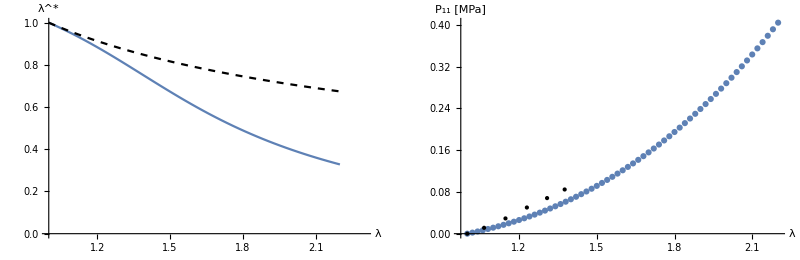

```mathematica
Do[
ptlist={};
λ0guess=1.;
Do[
Module[{k0=0.02,α=2.2,k=0.001,mg=1,k1=0.028 3096,k2=5.431*^-4,(*k3=0.1,*)pts,λ1,λ2,λ3,J,ζij},
J[λa_,λs_,λn_]:=λa λs λn;
ζij[λ1_,λ2_,λ3_]:=λ1^2 λ2^(2+α)+λ1^2 λ3^(2+α)+λ2^2 λ3^(2+α)+λ2^2 λ1^(2+α)+λ3^2 λ1^(2+α)+λ3^2 λ2^(2+α);
S11[λ1_,λ2_,λ3_]:=k0 -(k0+2k J[λ1,λ2,λ3](J[λ1,λ2,λ3]-1))/λ1^2+k1( ⅇ^(k2(λ1^2-1))-1)+2k3 If[ζij[λ1,λ2,λ3]>6, ⅇ^(mg(ζij[λ1,λ2,λ3]-6))-1,0](λ2^(2+α)+λ3^(2+α)+(2+α)/2 λ1^α(λ2^2+λ3^2));
S33[λ1_,λ2_,λ3_]:=k0 -(k0+2k J[λ1,λ2,λ3](J[λ1,λ2,λ3]-1))/λ3^2+2k3 If[ζij[λ1,λ2,λ3]>6, ⅇ^(mg(ζij[λ1,λ2,λ3]-6))-1,0](λ1^(2+α)+λ2^(2+α)+(2+α)/2 λ3^α(λ1^2+λ2^2));
pts={λ,Abs@λT}/.FindRoot[Evaluate[S33[λ,λT,λT]],{λT,λ0guess},MaxIterations->1000];
λ0guess=pts[[2]];
AppendTo[ptlist,pts];
]
,{λ,1,2.2,0.02}];
intpFunc=Interpolation[ptlist,InterpolationOrder->1];
influVar[k3]=intpFunc;
S11List[k3]=Table[{λ,λ S11[λ,intpFunc[λ],intpFunc[λ]]},{λ,1,2.2,0.02}]
,{k3,k3List}];GraphicsRow[{Show[(*ListPlot[ptlist],*)Plot[{intpFunc[λ],1/(√λ)},{λ,1,2.2},BaseStyle->14,AxesLabel->{"λ","λ^*"},PlotRange->{{1,2.3},{0.,1.}},PlotStyle->{Automatic,Directive[Dashed,Black]}]],
ListPlot[S11List[k0List[[1]]],BaseStyle->14,AxesLabel->{"λ","P_11 [MPa]"},Epilog->Point[{dataεFb+1,dataPFb(*MPa*)}ᵀ[[1;;6]]]]
}]
```

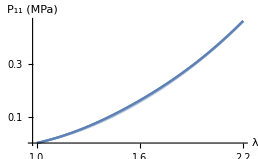
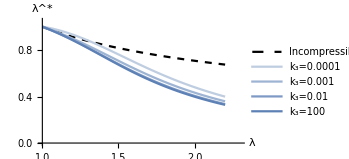
-Graphics- | -Graphics-

```mathematica
pltSty={Directive[Lighter[ColorData[97,1],0.6]],Directive[Lighter[ColorData[97,1],0.4]],Directive[Lighter[ColorData[97,1],0.2]],Directive[Lighter[ColorData[97,1],0.]]};

TableForm[{{
ListPlot[Table[S11List[α],{α,k3List}],Joined->True,BaseStyle->12,AxesLabel->{"λ","P_11 (MPa)"},
AxesStyle->Directive[Black,Thickness[Medium]],PlotStyle->pltSty,
Ticks->{{{1,"1.0"},1.2,1.4,1.6,1.8,{2,"2.0"},2.2},{0.1,0.2,0.3,0.4,0.5}},ImagePadding->{{3sizeLabels,sizeLabels},{1.5sizeLabels,2sizeLabels}},
ImageSize->Floor[(imgWidthTotal-1.5sizeLabels)/2]
],Plot[Evaluate@Prepend[Table[influVar[α][λ],{α,k3List}],1/(√λ)],{λ,1,2.2},BaseStyle->12,AxesLabel->{"λ","λ^*"},
AxesStyle->Directive[Black,Thickness[Medium]],PlotRange->{{1,2.3},{0.,1.05}},PlotStyle->Prepend[pltSty,Directive[Dashed,Black]],PlotLegends->Prepend[Table["k_3"<>"="<>ToString[α],{α,k3List}],"Incompressible"],
ImagePadding->{{3sizeLabels,sizeLabels},{1.5sizeLabels,2sizeLabels}},
ImageSize->Floor[(imgWidthTotal-1.5sizeLabels)/2]]}
}]
```